# Quantum Brownian Motion

## References

Path integral approach to quantum Brownian motion, by Caldeira and Leggett

["Reduction of a wave packet in quantum Brownian motion by Unruh and Zurek"](https://journals-aps-org.ezp.sub.su.se/prd/abstract/10.1103/PhysRevD.40.1071)

## Gaussian integral identity

-Graphics-
-Graphics-

```mathematica
Assuming[a>0&&b>0,Integrate[Exp[-(a x+b)^2],{x,-∞,∞}]]
```

(√π)/a

## Keldysh path integral for coherent bosons in a single quantum level

See Kamenev’s book, chapter 2 and 3

### Partition function definition

Define:

ρ̂ is an initial density matrix. We will choose it to be in thermal eq:
-Graphics- (notice that it is not normalized to unity)
and the unitary evolution operator:
-Graphics-

The trace is cyclic, and adding an identity operator expanded in a complete basis, i.e. OverHat[1]=∑_(i,j=1)^N |ϕ_i⟩  ⟨ϕ_i|,
and using the trace of a scalar is a scalar, then we have:
	 Tr A B=∑_(i,j=1)^N ⟨ϕ_j|A|ϕ_i⟩⟨ϕ_i|B|ϕ_j⟩

### Hamiltonian for bosonic particles in a single quantum state with energy ω_0

Consider:
-Graphics-=ω_0 N̂
then
-Graphics-,-Graphics-

### Path Integral steps

In order to derive the path integral formulation, let's divide the contour in the following way:
	-Graphics-

First, let's insert the over-complete coherent state basis:
	-Graphics-
at the initial and final states, then commute the integrals with the trace and then use the cyclic property of the trace:
	Tr U_C ρ  = ∫d[(ϕ̄)_1,ϕ_1]∫d[(ϕ̄)_(2N),ϕ_(2N)]ⅇ^(-|ϕ_1|^2-|ϕ_(2N)|^2) ⟨ϕ_1|U_c|ϕ_(2N)⟩    ⟨ϕ_(2N)|ρ|ϕ_1⟩ 

We can insert the over-complete basis at discrete infinitesimal time intervals, in order to derive the path integral:
For example, for N=3:
	-Graphics-
or more generally:
	⟨ϕ_1|(ρ̂)_0|ϕ_(2N)⟩ 
{ ∏_(j=1)^(N-1) ⟨ϕ_(j+1)|(Û)_δ_t|ϕ_j⟩}
⟨ϕ_N|1|ϕ_(N+1)⟩  
{∏_(j=N)^(2N-1) ⟨ϕ_(j+1)|(Û)_-δ_t|ϕ_j⟩}
Up to linear order in δ_t:
	-Graphics-
This actually applies to any normally-ordered H. -> Other examples? 

Use the identity:
	⟨ϕ_1|(ρ̂)_0|ϕ_(2N)⟩=exp{(ϕ̄)_1 ϕ_(2N)ρ(ω_0)}
and that
	-Graphics-
we derive the partition function below.

### Partition function discrete

-Graphics-
Note that G is non-diagonal, and it depends on the Hamiltonian. 
For N=3:
 -Graphics-, -Graphics-
Its inverse gives the 2-pt correlation functions.

### 2-pt correlation functions, discrete

-Graphics-
 For N=3, we get
 -Graphics-, ρ=ρ(ω_0)

### 2-pt correlation functions in the continuum limit: N→ ∞, ϕ_i→ ϕ(t)

Determinant in the continuum limit:
	-Graphics-
2-pt functions (+ and - indicate the positive and the negative branches of the Keldysh contour.):
	-Graphics-
where the bosonic occupation number is:
	-Graphics-

### Green functions in the continuum limit and Keldysh space

Keldysh rotation:
	-Graphics-
2-pt correlation functions:
	-Graphics-
	-Graphics-
	-Graphics-
Properties 
	-Graphics-

### Fluctuation-Dissipation Theorem: G^K(ϵ)=Coth[(ϵ-μ)/(2 T)](G^R(ϵ)-G^A(ϵ))

For a thermal initial state, 
	n_B=1/(e^((ϵ-μ)/T)-1)
and using the delta identity:
	∫_(-∞)^∞ e^(ⅈ ω t)ⅆt = 2 π δ(ω) =ⅈ(1/(ω +ⅈ 0)-1/(ω -ⅈ 0))
	∫_0^∞ e^((ⅈ ω-0) t)ⅆt =ⅈ/(ω +ⅈ 0)
	∫_(-∞)^0 e^((ⅈ ω+0) t)ⅆt =-ⅈ/(ω -ⅈ 0)
we can rewrite:
	G^K(ϵ)=-2π ⅈ (2/(e^((ϵ-μ)/T)-1)+1)δ(ϵ-ω_0)
	=- ⅈ ((e^((ϵ-μ) /T)+1)/(e^((ϵ-μ)/T)-1))ⅈ(1/(ϵ-ω_0 +ⅈ 0)-1/(ϵ-ω_0 -ⅈ 0))
	=Coth[(ϵ-μ)/(2 T)](G^R(ϵ)-G^A(ϵ))

### Nonlinear Fluctuation-Dissipation Theorem

Higher order correlation functions in Keldysh space are not all independent of each other, just like in the 2-pt case. See:

[A Generalized Fluctuation-Dissipation Theorem for NonlinearResponse Functions](https://arxiv.org/pdf/hep-th/9809016.pdf)

### Partition function in the continuum limit

Partition function is formally:
	-Graphics-	

The naive way gives a non-interacting action. Taking into account the 2-pt correlation functions: 
	-Graphics-

## Keldysh action for the harmonic oscillator

### Classical action along the Keldysh contour S[X^cl, x^q]=2∫_C dt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q)

Single particle in an arbitrary potential, where C is the Keldysh closed time contour:
-Graphics-
Splitting the contour in the + and - branches:
	S[X_+, x_-]=∫_(-∞)^∞ ⅆt [2(Ẋ)^cl(Ẋ)^q-V(X_+)+V(X_-)]
then do the Keldysh rotation:
-Graphics-
The action becomes ()after a partial integration for the 1st term):
-Graphics-

#### Harmonic oscillator

V(X)=ω_0/2 X^2
S[X^cl, x^q]=2∫_C dt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q)

#### Small X^q expansion

-Graphics-
V’(X) is derivative respective X

### Keldysh action S[X^cl,X^q]=2∫_(-∞)^∞ ⅆt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q+1/4 X^q D^(-1K) X^q)

The Keldysh action takes into account the 2-pt correlation between the fields of the different branches (see the previous section, where the structure of the action applies here too):
	-Graphics-
	-Graphics-

#### Green functions for the harmonic oscillator

-Graphics-

In Fourier space:
-Graphics-
-Graphics-

D^K(ϵ)=1/2 Coth(ϵ/(2 T))[1/((ϵ+ⅈ 0)^2-ω_0^2)-1/((ϵ-ⅈ 0)^2-ω_0^2)]-> In time space? The textbook says it's only a regularization...

#### Action for the harmonic oscillator

D^-1 X=(D^(-1A) X^q, D^(-1R) X^cl+D^(-1K) X^q)
	=2(-(X^(..))^q-ω_0^2 X^q, -(X^(..))^cl-ω_0^2 X^cl+1/2 D^(-1K) X^q)

1/2 X^T D^-1 X =1/2(X^cl D^(-1A) X^q+ X^q D^(-1R) X^cl+X^q D^(-1K) X^q)
		=(-X^cl(X^(..))^q-ω_0^2 X^cl X^q-X^q (X^(..))^cl-ω_0^2 X^q X^cl+1/2 X^q D^(-1K) X^q)
		{d/dt(X^cl(Ẋ)^q)=(Ẋ)^cl(Ẋ)^q+X^cl(X^(..))^q, d/dt((Ẋ)^cl X^q)=(Ẋ)^cl(Ẋ)^q+(X^(..))^cl X^q}
                   → 2((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q+1/4 X^q D^(-1K) X^q)

The last term in red is an additional term that corrects the action if the continuum limit is done naively. It's of higher order in X^q, so it can be ignored in the semiclassical limit.

#### Quartic potential?

V(X) =λ X^4
V(X_+=X^cl+X^q)-V(X_-=X^cl-X^q)=8λ (X^(cl 3)X^q+X^cl X^(q 3))

```mathematica
(xc+xq)^4-(xc-xq)^4//Expand
```

8 xc^3 xq+8 xc xq^3

## Single particle linearly coupled with a bath

### Action

Note that S_p in the book is the classical action of the single particle! I think the Keldysh action should be used, and for the harmonic oscillator (see previous section):
	S_p[X^cl,X^q]=2∫_(-∞)^∞ ⅆt  ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q+1/4 X^q D^(-1K) X^q)

-Graphics-
σ_1is the Pauli matrix in Keldysh space

### Effective action for the single particle

S[X^cl,X^q]=1/2∫_(-∞)^∞ ⅆt  (X(t))^T D^-1(t)X(t)+1/2∫∫_(-∞)^∞ ⅆtⅆt'  X^T(t)𝔇^-1(t-t') X(t')
		=1/2∫∫_(-∞)^∞ ⅆtⅆt'  X^T(t){D^-1(t)δ(t-t')+𝔇^-1(t-t') }X(t')
where
	-Graphics-
	
We have integrated out S_bath+S_int using a Gaussian integral identity.

Using the results from the single harmonic oscillator in a previous section, we get for the bath:
	𝔇^-1=(0 | [𝔇^-1]^A
[𝔇^-1]^R | [𝔇^-1]^K)=∑_s g_s^2(0 | -1/([D_s^-1]^A)
-1/([D_s^-1]^R) | ([D_s^-1]^K)/(([D_s^-1]^R [D_s^-1])^A)) (in time space)

#### Computation details

```mathematica
{Xc,Xq}.({{0, DinvA}, {DinR, DinvK}}).{Xc,Xq}//Simplify
```

Xq (DinR Xc+DinvA Xc+DinvK Xq)

```mathematica
Dinv=({{0, DinvA}, {DinR, DinvK}});
Dmatrix=Inverse@Dinv;
%//MatrixForm
-PauliMatrix[1].Dmatrix.PauliMatrix[1]//MatrixForm
```

(-DinvK/(DinR DinvA) | 1/DinR
1/DinvA | 0)

(0 | -1/DinvA
-1/DinR | DinvK/(DinR DinvA))

### In Fourier space?

-Graphics-
-Graphics-

[D_s^-1(t)]^(R,A)=2((ⅈ ∂_t ± ⅈ 0)^2-ω_s^2)  
[𝔇^-1(t)]^(R,A)=-∑_s g_s^2 1/([D_s^-1]^(R,A))

[D_s^-1(ϵ)]^(R,A)=2((ϵ ± ⅈ 0)^2-ω_s^2)-> [D_s(ϵ)]^(R,A)=2((ϵ ± ⅈ 0)^2-ω_s^2)^-1
[𝔇^-1(ϵ)]^(R,A)=-∑_s g_s^2 2((ϵ ± ⅈ 0)^2-ω_s^2)^-1=∫_0^∞ ⅆω/(2 π)ω J(ω)  1/(ω^2-(ϵ ± ⅈ 0)^2)

[𝔇^-1(t)]^(R,A)=∓∫_0^∞ ⅆω J(ω) Sin[t ω]
	∫_(-∞)^∞ ⅆϵ 1/(ω^2-(ϵ ± ⅈ 0)^2)Exp[ⅈ ϵ t] = ∫_(-∞)^∞ ⅆϵ 1/((ϵ ± ⅈ 0)+ω)-1/((ϵ ± ⅈ 0)-ω)Exp[ⅈ ϵ t]=∓(2 π Sin[t ω])/ω
	(∫_(-∞)^∞ ⅆϵ 1/(ω^2-(ϵ ± ⅈ 0)^2)Exp[-ⅈ ϵ t]=±(2 π Sin[t ω])/ω)
		poles
			ϵ_+=ω ∓ ⅈ 0
			ϵ_-=-ω ∓ ⅈ 0
		when the poles are in the lower half plane, then there's a global negative sign  because of the orientation

[𝔇^-1(t)]^R+[𝔇^-1(t)]^A=0
[𝔇^-1(t)]^R-[𝔇^-1(t)]^A=-2∫_0^∞ ⅆω J(ω) Sin[t ω]

How to compute the K-component?
[D_s(ϵ)]^K=Coth(ϵ/T)([D_s(ϵ)]^R-[D_s(ϵ)]^A)
[𝔇^-1(ϵ)]^K=∑_s g_s^2([D_s^-1]^K)/(([D_s^-1]^R [D_s^-1])^A)=∑_s g_s^2 1/((([D_s^-1]^R [D_s^-1])^A[D_s])^K)
		=∑_s g_s^2 1/(([D_s^-1]^R [D_s^-1])^A)1/(Coth(ϵ/T)([D_s]^R-[D_s]^A))
		=∑_s g_s^2 1/(Coth(ϵ/T)([D_s^-1]^A-[D_s^-1]^R))
		=∑_s g_s^2 1/(Coth(ϵ/T)(2((ϵ - ⅈ 0)-ω)-2((ϵ + ⅈ 0)-ω)))=∑_s g_s^2-1/(Coth(ϵ/T)4  ⅈ 0) ?

𝔇^K(ϵ)=Coth[ϵ/(2 T)](𝔇^R(ϵ)-𝔇^A(ϵ))

#### Computation

```mathematica
2π ⅈ Plus@@{Residue[Exp[ⅈ ϵ t]/(ω^2-(ϵ+ⅈ x)^2),{ϵ,-ω-ⅈ x}],Residue[Exp[ⅈ ϵ t]/(ω^2-(ϵ+ⅈ x)^2),{ϵ,ω-ⅈ x}]}/.x->0
%//FullSimplify
2π ⅈ Plus@@{Residue[Exp[ⅈ ϵ t]/(ω^2-(ϵ-ⅈ x)^2),{ϵ,-ω+ⅈ x}],Residue[Exp[ⅈ ϵ t]/(ω^2-(ϵ-ⅈ x)^2),{ϵ,ω+ⅈ x}]}/.x->0
%//FullSimplify
```

2 ⅈ π (ⅇ^(-ⅈ t ω)/(2 ω)-ⅇ^(ⅈ t ω)/(2 ω))

(2 π Sin[t ω])/ω

2 ⅈ π (ⅇ^(-ⅈ t ω)/(2 ω)-ⅇ^(ⅈ t ω)/(2 ω))

(2 π Sin[t ω])/ω

### Solution for the Ohmic bath

Assuming continuous spectrum for the bath and that it’s ohmic, i.e.
	-Graphics-

Then we get:

	-Graphics-
At high T limit, the local term is the leading one.

#### Ohmic bath computation details

-Graphics-
-Graphics- const may be obmitted
-Graphics-
Inverse FT the expressions above
	-Graphics- -> gives dissipation
	-Graphics--> gives noise fluctuation
	-Graphics- satisfies the condition
	-Graphics-

[D_eff^-1]^(R,A)(t-t')=[D^-1]^(R,A)(t)δ(t-t')+[𝔇^-1]^(R,A)(t-t')
			=2[(ⅈ∂_t ± ⅈ 0)^2-ω_0^2∓ γ ∂_t']δ(t-t') 


[D_eff^-1]^K(t-t')=[D^-1]^K(t)δ(t-t')+[𝔇^-1]^K(t-t')
			=4 ⅈ γ [(2 T+C) δ(t-t')-(π T^2)/(Sinh(π T (t-t')))]

	D^K(ϵ)=1/2 Coth(ϵ/(2 T))[1/((ϵ+ⅈ 0)^2-ω_0^2)-1/((ϵ-ⅈ 0)^2-ω_0^2)]?

```mathematica
Series[Coth[x],{x,0,1}]
```

1/x+x/3+O[x]^2

##### High T limit

[𝔇^-1(t-t')]^K≈8 ⅈ γ T δ(t-t')
	T^2/Sinh[π T t]^2=(2 T^2)/(-1+1/2 ⅇ^(-2 π t T)+1/2 ⅇ^(2 π t T))≈4 T^2 ⅇ^(-2 π t T)

## Effective field approach: a free particle interacting with a bath

```mathematica
["Hong-Liu's lecture notes"](https://arxiv.org/pdf/1805.09331.pdf), page 12
```

Note that the particle here is free, namely V(X)=0. However, when the guess the L_EFT, the use general arguments, and do get a term that actually would correspond to the harmonic potential. See more comments below.

```mathematica
-Graphics-
-Graphics-
```

Comparing the above result with the exact result in the previous section, we see that:
	The c x_a x_r term comes from a quadratic potential, but Hong Liu says it’s an effective potential induced by the bath?
	The ν x_a (ẋ)_r and the i/2 σ x_a^2 terms come from integrating out the bath.
	The M̃(ẋ)_a (ẋ)_r term comes from the kinetic term.

Most general terms :
x_a^2 → gives rise the Gaussian noise
x_r^2 → Not there, because of the Lagrangian? ...
x_a x_r
(ẋ)_a x_r → Not there
x_a(ẋ)_r
(ẋ)_a(ẋ)_r

```mathematica
Series[1/(1-x),{x,0,1}]
```

1+x+O[x]^2

### Remark for higher order terms

### Cubic terms

Most general terms :
x_a^3
x_r^3 → should not be there
x_a^2 x_r
x_a x_r^2
((ẋ)_a)^2 x_r
x_a((ẋ)_r)^2
(ẋ)_a x_r^2
x_a^2(ẋ)_r
((ẋ)_a)^2(ẋ)_r
(ẋ)_a((ẋ)_r)^2

### Stochastic equation for some cubic terms such that the noise is Gaussian

Legendre transformation to get the Gaussian noise ξ :

Then, the argument of the exponential is:
	-c x_a x_r -ν x_a (ẋ)_r+M̃(ẋ)_a (ẋ)_r+i/(2σ) ξ^2+ξ x_a
- α x_a x_r^2 - β x_a((ẋ)_r)^2- γ (ẋ)_a x_r^2 
	
For simplicity, we consider non-linear interactions that are linear in x_a, as shown in the line above.
Now, we can derive the SDE:
	c  x_r +ν (ẋ)_r+M̃(x^(..))_r+α x_r^2+β ((ẋ)_r)^2-2γ x_r(ẋ)_r=ξ
What are the meanings of the new terms? Are they physical?

### Non Gaussian noise?

## Linear QBM exact quantum master eq

### Setting

Master equation is the time evolution of the (reduced) density matrix:
-Graphics-
The goal is to find H_ρ operator.

#### Feynman-Vernon

Assuming the initial density matrix can be factorized to the one of the Brownian motion particle, i.e. ρ_r, and that of the bath, 
-Graphics-
then:
-Graphics-
where J_r is an evolution operator, with the path-integral representation:
-Graphics-
F[x,x'] is called the influence functional, which contains the bath dof and the interaction with the bath (it contains the initial bath density matrix too).
The bath's initial density matrix will be assumed to be in thermal eq.

#### Action

-Graphics-

#### Spectral density: I(ω)=2/π Μ γ_0 ω (ω/(ω̃))^(n-1)Exp[-ω^2/Λ^2]

The spectral density is defined as:
-Graphics-
We study the ones that have the shape:
-Graphics-

{{√10 ⅇ^(-ω^2/100) √ω,ⅇ^(-ω^2/100) ω,1/100 ⅇ^(-ω^2/100) ω^3}}

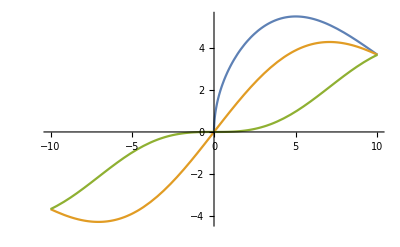

```mathematica
ω (ω/Λ)^{n-1} Exp[-ω^2/Λ^2]/.n->{1/2,1,3}/.Λ->10
Plot[Evaluate@%,{ω,-10,10}]
```

### Influence functional, fluctuation-dissipation η(s)=-∫_0^∞ ⅆω I(ω) sin(ω s) ν(s)=∫_0^∞ ⅆω I(ω) coth(1/2 β ℏ ω) cos(ω s)

ln F[x,x']=-ⅈ/ħ ∫_0^t ds_1∫_0^s_1 ds_2{x_q(s_1)η(s_1-s_2) x_cl(s_2) -ⅈ x_q(s_1)ν(s_1-s_2) x_q(s_2)}
z	
Noise or fluctuation kernel is non-local in general:
-Graphics-

Dissipation kernel: η(s)=-∫_0^∞ ⅆω I(ω)  sin(ω s)
-Graphics-, -Graphics-

Fluctuation-dissipation relation:
-Graphics-

#### Check the FD relation?

⋁[ω,s]=I[ω]Coth[1/2 β ℏ ω]Cos[ω s]
K[ω,s]=ω/π Coth[1/2 β ℏ ω]Cos[ω s]
γ[ω,s]=1/ω I[ω]Cos[ω s]

⋁[ω,s]=π K[ω,s]γ[ω,s] /Cos[ω s]
=∫_(-∞)^∞ ⅆs' ∫_0^∞ ⅆω' K[ω,s-s']γ[ω',s']

⋁[s]=∫_(-∞)^∞ ⅆs'  K[s-s']γ[s']
	=∫_(-∞)^∞ ⅆs'∫_0^∞ ⅆω ∫_0^∞ ⅆω' K[ω,s-s']γ[ω',s']
	=∫_(-∞)^∞ ⅆs'∫_0^∞ ⅆω ∫_0^∞ ⅆω' ω/π Coth[1/2 β ℏ ω]Cos[ω (s-s')]1/ω' I[ω']Cos[ω' s']
	=∫_0^∞ ⅆω ∫_0^∞ ⅆω' ω/π Coth[1/2 β ℏ ω]1/ω' I[ω']∫_(-∞)^∞ ⅆs'Cos[ω (s-s')]Cos[ω' s']

### High T limit ν(s)=2/(β ℏ) γ(s)=2/(β ℏ)∫_0^∞ ⅆω (I(ω))/ω cos(ω s) η(s)=γ'(s)=-∫_0^∞ ⅆω I(ω) sin(ω s)

Classical or high T limit:
	-Graphics-

Derivation:
	coth(1/2 β ℏ ω) ≈2/(β ℏ ω) +O(β)=(2 T)/(ℏ ω)

K(s)=∫_0^∞ ⅆω/π ω  coth(1/2 β ℏ ω) cos(ω s)
	≈1/π  2/(β ℏ)∫_0^∞ ⅆω cos(ω s)
	=1/π  1/(β ℏ)2π δ(s)=2/(β ℏ) δ(s)
ν(s)=∫_(-∞)^∞ ds' K(s-s') γ(s')
	≈2/(β ℏ)∫_(-∞)^∞ ds' δ(s-s') γ(s')=2/(β ℏ) γ(s)

```mathematica
Series[Coth[x],{x,0,1}]
```

1/x+x/3+O[x]^2

### Exact quantum master equation

-Graphics-

#### Coefficients

-Graphics-
u and v are classical solutions, see the paper
-Graphics-
-Graphics-

#### High T limit of the coefficients: why doesn’t the 2nd diffusion term go to 0 for ohmic case?

```mathematica
-Graphics--Graphics-
```

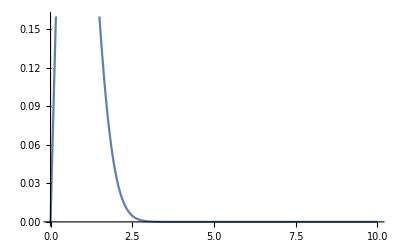

```mathematica
Plot[Λ Exp[-Λ^2],{Λ,0,10}]
```

### Exact Wigner equation

This paper corrects the equation above adding ħ in front of the diffusion coefs.
["https://arxiv.org/pdf/quant-ph/9508004.pdf"](https://arxiv.org/pdf/quant-ph/9508004.pdf)

### Langevin eqs

#### FP coefficients

D_q=p
D_p=-(Ω^2+(δΩ(t))^2) q-Γ(t) p
D_pp=2 ħ Γ(t) h(t)
D_pq=D_qp=-ħ Γ(t) f(t)

#### FP <-> Langevin

Risken book, chapter 3.4.
Langevin to FP transformation below determines uniquely Ds:
	-Graphics-
	-Graphics-
	
FP to Langevin (with white noise) is not unique for N>1. For N=2 case, which is our case, there’s an additional degree of freedom. 
In the eigenbasis of the diffusion matrix:
	-Graphics-
In our case the diffusion matrix doesn’t depend on the (q, p), and we denote the eigenbasis with ', hence
	h'_i=D'_i
g'_(i j)= √(D'_(i j))

#### Eigenbasis

D=(0 | D_qp
D_qp | D_pp)
λ_±=1/2 (D_pp±√(D_pp^2+4 D_qp^2)) 
v_±={-λ_∓/D_qp,1}
Λ=( v_- v_+)=(-λ_+/D_qp | -λ_-/D_qp
1 | 1)
D'=Λ^T D Λ -> D =(Λ^-1)^T D' Λ^-1
g'=√D' -> g = (Λ^-1)^T g' Λ^-1 -> the structure is not the same as D, namely g_11!=0 in general. Can we rotate it away?


D_(1)'=Λ^T D_(1)=h'
h = (Λ^-1)^T h'=D_(1)

##### Computations

```mathematica
Inverse@({{Λ1, Λ2}, {1, 1}})//MatrixForm
```

(1/(Λ1-Λ2) | -Λ2/(Λ1-Λ2)
-1/(Λ1-Λ2) | Λ1/(Λ1-Λ2))

```mathematica
dm=({{0, Dqp}, {Dqp, Dpp}});
ee=Eigenvalues@dm
ev=Eigenvectors@dm
```

{1/2 (Dpp-√(Dpp^2+4 Dqp^2)),1/2 (Dpp+√(Dpp^2+4 Dqp^2))}

{{-(Dpp+√(Dpp^2+4 Dqp^2))/(2 Dqp),1},{-(Dpp-√(Dpp^2+4 Dqp^2))/(2 Dqp),1}}

```mathematica
toλRule={(Plus@@ee//Simplify)-> λ1+λ2,(ee[[2]]-ee[[1]]//Simplify)-> λ2-λ1}
invλRule={λ1-> ee[[1]],λ2->ee[[2]]}
λ1 λ2/.invλRule//FullSimplify
toλRule=Append[toλRule,-%-> -λ1 λ2]
```

{Dpp→λ1+λ2,√(Dpp^2+4 Dqp^2)→-λ1+λ2}

{λ1→1/2 (Dpp-√(Dpp^2+4 Dqp^2)),λ2→1/2 (Dpp+√(Dpp^2+4 Dqp^2))}

-Dqp^2

{Dpp→λ1+λ2,√(Dpp^2+4 Dqp^2)→-λ1+λ2,Dqp^2→-λ1 λ2}

```mathematica
evλ=ev/.toλRule
norms=({evλ[[1]].evλ[[1]],evλ[[2]].evλ[[2]]}//Simplify)
nevλ=Assuming[Dpp>0&&Dqp>0,evλ/√norms/.toλRule//FullSimplify]
```

{{-λ2/Dqp,1},{-λ1/Dqp,1}}

{1+λ2^2/Dqp^2,1+λ1^2/Dqp^2}

{{-λ2/(√(Dqp^2+λ2^2)),Dqp/(√(Dqp^2+λ2^2))},{-λ1/(√(Dqp^2+λ1^2)),Dqp/(√(Dqp^2+λ1^2))}}

```mathematica
nevλ.dm.Transpose[nevλ]/{λ1,λ2}/.toλRule/.invλRule//FullSimplify
```

{{1,0},{0,1}}

```mathematica
inevλ=Assuming[Dpp>0&&Dqp>0,Inverse@nevλ//FullSimplify]/.toλRule//Simplify
```

{{(√(λ2 (-λ1+λ2)))/(λ1-λ2),(√(λ1 (λ1-λ2)))/(-λ1+λ2)},{(λ1 √(λ2 (-λ1+λ2)))/(Dqp (λ1-λ2)),(√(λ1 (λ1-λ2)) λ2)/(Dqp (-λ1+λ2))}}

```mathematica
gd=DiagonalMatrix@{√λ1,√λ2}
Assuming[Dpp>0&&Dqp>0,inevλ.gd.Transpose@inevλ//FullSimplify]
%/.invλRule//Simplify
```

{{√λ1,0},{0,√λ2}}

{{√λ1-λ1/(√λ1+√λ2),-(λ1 λ2)/(Dqp √λ1+Dqp √λ2)},{-(λ1 λ2)/(Dqp √λ1+Dqp √λ2),-(λ1 λ2 (λ1+√λ1 √λ2+λ2))/(Dqp^2 (√λ1+√λ2))}}

{{(√(Dpp-√(Dpp^2+4 Dqp^2)) √(Dpp+√(Dpp^2+4 Dqp^2)))/(√2 (√(Dpp-√(Dpp^2+4 Dqp^2))+√(Dpp+√(Dpp^2+4 Dqp^2)))),(√2 Dqp)/(√(Dpp-√(Dpp^2+4 Dqp^2))+√(Dpp+√(Dpp^2+4 Dqp^2)))},{(√2 Dqp)/(√(Dpp-√(Dpp^2+4 Dqp^2))+√(Dpp+√(Dpp^2+4 Dqp^2))),(2 Dpp+√(Dpp-√(Dpp^2+4 Dqp^2)) √(Dpp+√(Dpp^2+4 Dqp^2)))/(√2 (√(Dpp-√(Dpp^2+4 Dqp^2))+√(Dpp+√(Dpp^2+4 Dqp^2))))}}

```mathematica
RotationMatrix[θ].({{a, c}, {c, d}}).Transpose@RotationMatrix[θ]//FullSimplify
Solve[%[[1,1]]==0,θ]//FullSimplify
```

{{a Cos[θ]^2-2 c Cos[θ] Sin[θ]+d Sin[θ]^2,c Cos[2 θ]+(a-d) Cos[θ] Sin[θ]},{c Cos[2 θ]+(a-d) Cos[θ] Sin[θ],d Cos[θ]^2+a Sin[θ]^2+c Sin[2 θ]}}

{{θ→ConditionalExpression[2 π C[1]-ⅈ Log[-(ⅈ (c^2-ⅈ c d+√(c^4-a c^2 d)) √(d^2/(2 c^2-a d+d^2+2 √(c^4-a c^2 d))))/(c d)], C[1]∈ℤ]},{θ→ConditionalExpression[2 π C[1]-ⅈ Log[((c (ⅈ c+d)+ⅈ √(c^4-a c^2 d)) √(d^2/(2 c^2-a d+d^2+2 √(c^4-a c^2 d))))/(c d)], C[1]∈ℤ]},{θ→ConditionalExpression[2 π C[1]-ⅈ Log[(ⅈ (-c^2+ⅈ c d+√(c^4-a c^2 d)) √((2 c^2-a d+d^2+2 √(c^4-a c^2 d))/(4 c^2+(a-d)^2)))/(c d)], C[1]∈ℤ]},{θ→ConditionalExpression[2 π C[1]-ⅈ Log[((c (ⅈ c+d)-ⅈ √(c^4-a c^2 d)) √((2 c^2-a d+d^2+2 √(c^4-a c^2 d))/(4 c^2+(a-d)^2)))/(c d)], C[1]∈ℤ]}}

#### Wrong

q̇= p+√(- ħ Γ(t) f(t))ξ_p
ṗ=-(Ω^2+(δΩ(t))^2)q-Γ(t) p+√(ħ Γ(t) f(t))ξ_p+√(-ħ Γ(t) f(t)) ξ_q

q^(..)= -(Ω^2+(δΩ(t))^2)q
	-Γ(t) (q̇-√(- ħ Γ(t) f(t))ξ_p)
          +√(2ħ Γ(t) h(t))ξ_p+√(-ħ Γ(t) f(t)) (ξ_q+ξ_p)+∂/(∂t)(√(-ħ Γ(t) f(t))ξ_p)
Assume
	q^(..) ≈0
then
Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q
	      + (Γ(t) √(- ħ Γ(t) f(t))+√(2ħ Γ(t) h(t))+√(-ħ Γ(t) f(t))+∂/(∂t)(√(-ħ Γ(t) f(t))))ξ_p
                   +√(-ħ Γ(t) f(t))OverDot[ξ_p]
                   +√(-ħ Γ(t) f(t)) ξ_q

which can be written as
	Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q +√(-ħ Γ(t) f(t))η+√(-ħ Γ(t) f(t)) ξ_q
	          η≡ (Γ(t) +√(-2 h(t)/f(t))+1+(Γ̇(t))/(2 Γ(t))+(ḟ(t))/(2 f(t)))ξ_p+√(-ħ Γ(t) f(t))OverDot[ξ_p]


Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q+ (Γ(t) ϵ+√(2ħ Γ(t) h(t))+ϵ+∂/(∂t)ϵ)ξ_p+ ϵ OverDot[ξ_p]+ ϵ ξ_q

Assume ϵ=√(-ħ Γ(t) f(t)) and ϵ̇=0, then, at leading order
	        η= (Γ(t) +(√(2ħ Γ(t) h(t)))/ϵ+1)ξ_p+ϵ OverDot[ξ_p]≈(√(2ħ Γ(t) h(t)))/ϵ ξ_p
	       Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q +√(-ħ Γ(t) f(t))η+√(-ħ Γ(t) f(t)) ξ_q

##### Computations

```mathematica
1/(√(-ħ Γ[t] f[t]))D[√(-ħ Γ[t] f[t]),t]//Expand
```

f'[t]/(2 f[t])+Γ'[t]/(2 Γ[t])

```mathematica
eq[t_]=a[t] ξ[t]+b[t]ξ'[t];

Solve[η[t]==eq[t],ξ'[t]]//Flatten
η'[t]-eq'[t]/.%//Simplify
Collect[Solve[%==0,η'[t]],{η[t],ξ[t],ξ'[t]}, Simplify]
%/.a->Function[t,aconst]/.b->Function[t,bconst]
```

{ξ'[t]→(η[t]-a[t] ξ[t])/b[t]}

(a[t] (-η[t]+a[t] ξ[t]))/b[t]-ξ[t] a'[t]-((η[t]-a[t] ξ[t]) b'[t])/b[t]+η'[t]-b[t] ξ''[t]

{{η'[t]→(η[t] (a[t]+b'[t]))/b[t]-(ξ[t] (a[t]^2-b[t] a'[t]+a[t] b'[t]))/b[t]+b[t] ξ''[t]}}

{{η'[t]→(aconst η[t])/bconst-(aconst^2 ξ[t])/bconst+bconst ξ''[t]}}

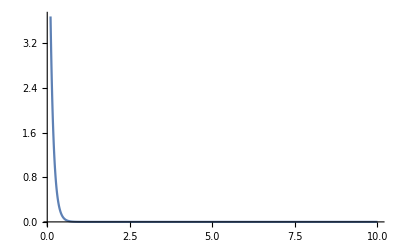

```mathematica
Plot[Exp[-δt / τ]/τ/.τ->0.1,{δt,0.1,10},PlotRange->All]
```

### Pure ohmic case: Unruh-Zurek

Pure ohmic (it’s unphysical because it has no cutoff): 
 -Graphics-

#### Master eq

-Graphics-

#### Coefficients

```mathematica
-Graphics-
-Graphics-
-Graphics-
-Graphics-
```

```mathematica
Series[Coth[β ω/2],{β,0,1}]
```

2/(ω β)+(ω β)/6+O[β]^2

```mathematica
Integrate[1/π ω 2/(ω β) Cos[ω t],{ω,0,Λ}]
Integrate[% Sin[Ω t]Exp[-γ t],t] 
Assuming[t>0&&Ω>0,Series[%,{Λ,∞,0}]//FullSimplify]
```

(2 Sin[t Λ])/(π t β)

1/(2 π β)(ExpIntegralEi[-t (γ-ⅈ (Λ-Ω))]+ExpIntegralEi[-t (γ+ⅈ (Λ-Ω))]-ExpIntegralEi[-t γ-ⅈ t (Λ+Ω)]-ExpIntegralEi[-t γ+ⅈ t (Λ+Ω)])

(ⅇ^(-ⅈ t Λ-t (γ-ⅈ Ω)+O[1/Λ]^2)+ⅇ^(-ⅈ t Λ-t (γ+ⅈ Ω)+O[1/Λ]^2)+ⅇ^(ⅈ t Λ-t (γ+ⅈ Ω)+O[1/Λ]^2)+ⅇ^(ⅈ t Λ+(-t γ+ⅈ t Ω)+O[1/Λ]^2)) O[1/Λ]^1

```mathematica
Exp[-ⅈ t Λ-t (γ-ⅈ Ω)]+Exp[-ⅈ t Λ-t (γ+ⅈ Ω)]+Exp[ⅈ t Λ-t (γ+ⅈ Ω)]+Exp[ⅈ t Λ-t (γ-ⅈ Ω)]//FullSimplify
```

4 ⅇ^(-t γ) Cos[t Λ] Cos[t Ω]

#### From Unruh-Zurek paper

-Graphics-
-Graphics-
-Graphics-

### Markovian case: Caldeira-Leggett (ohmic & at high T)

-Graphics-
From the original Caldeira-Leggett paper, at hight  T  limit:s
-Graphics-
It looks like there's one ħ discrepancy between Caldeira-Legget and the Hu-Path-Zhang paper. I guess Caldeira-Legget is correct, since it gives the right D in the classical limit.

### Wigner equation for the Markovian case, my derivation

The ħ in the diffusion term should be gone. This result is consistent with Caldeira-Leggett.

#### ∂/(∂ t)W(x,p,t)= (-∂/(∂ x){p}+∂/(∂ p){Ω^2 x+2 γ_0 p}+2 γ_0 k_B T ħ∂^2/(∂ p^2))W(x,p,t)

H =1/2 p^2+1/2 Ω^2 x^2
{H, W} =(∂ H)/(∂ x)(∂ W)/(∂ p)-(∂ H)/(∂ p) (∂ W)/(∂ x)=Ω^2 x(∂ W)/(∂ p)-p(∂ W)/(∂ x)

```mathematica
{ħ^2(-ⅈ/ħ),-Ω^2 x (- ⅈ ħ),-2ⅈ ħ γ (-1),-ⅈ 2 k T γ (-ħ^2)}/(ⅈ ħ)
```

{-1,x Ω^2,2 γ,2 ħ k T γ}

#### Langevin equations: ẋ=p ṗ=-2 γ_0 p -Ω^2 x+ξ(t)s

We set m=1

Fokker-Planck (Kramer’s equation):
-Graphics-
-Graphics-(α=γ)

#### ⅈ ħ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t) ={ħ^2∂^2/(∂ x∂ Δ)-Ω^2 x Δ-2ⅈ ħ γ_0 Δ∂/(∂ Δ)-ⅈ 2 k_B T γ_0 Δ^2}ρ_r(x-Δ/2,x+Δ/2,t)

Change of variables:
 y→ x-Δ/2, y'→ x+Δ/2
the inverse transformation is (looks like Keldysh rotation!):
x→ 1/2(y+y') ,Δ→ y'-y
ⅈ ħ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t) ={ħ^2∂^2/(∂ x∂ Δ)-Ω^2 x Δ-2ⅈ ħγ_0 Δ∂/(∂ Δ)-ⅈ 2 k_B Tγ_0 Δ^2}ρ_r(x-Δ/2,x+Δ/2,t)

y-y'=-Δ
y^2-y'^2=-2 x Δ
(y-y')^2=Δ^2
(∂/(∂ y)-∂/(∂ y'))ρ_r(y,y',t) =-2∂/(∂ Δ)ρ_r(y(x,Δ),y'(x,Δ),t)
(∂^2/(∂ y^2)-∂^2/(∂ y'^2))ρ_r(y,y',t) =-2∂^2/(∂ x∂ Δ)ρ_r(y(x,Δ),y'(x,Δ),t)

	∂/(∂ y)ρ_r(y,y',t)={(∂ x)/(∂ y)∂/(∂ x)+(∂ Δ)/(∂ y)∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
                                              ={1/2∂/(∂ x)-∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
	∂/(∂ y')ρ_r(y,y',t)={1/2∂/(∂ x)+∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
	∂^2/(∂ y^2)ρ_r(y,y',t)={1/2∂/(∂ x)-∂/(∂ Δ)}^2 ρ_r(y(x,Δ),y'(x,Δ),t)
              ∂^2/(∂ y'^2)ρ_r(y,y',t)={1/2∂/(∂ x)+∂/(∂ Δ)}^2 ρ_r(y(x,Δ),y'(x,Δ),t)

(∂/(∂ y)+∂/(∂ y'))ρ_r(y,y',t) =∂/(∂ x)ρ_r(y(x,Δ),y'(x,Δ),t)

```mathematica
{y-yp,y^2-yp^2,(y-yp)^2}/.{y-> (x-Δ/2),yp-> (x+Δ/2)}//FullSimplify
```

{-Δ,-2 x Δ,Δ^2}

#### ∂/(∂ Δ)→-ⅈ/ħ p, Δ→- ⅈ ħ ∂/(∂ p) , Δ∂/(∂ Δ)→- ∂/(∂ p) p, Δ^2→-ħ^2∂^2/(∂ p^2)

W(x,p,t)=∫ d Δ  exp(ⅈ/ħ p Δ)   ρ_r(x-Δ/2,x+Δ/2,t)
∂/(∂ t)W(x,p,t)=∫ d Δ  exp(ⅈ/ħ p Δ) ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t)
We can use the replaments:
exp(ⅈ/ħ p Δ)  Δ→  -ⅈ ħ∂/(∂ p)exp(ⅈ/ħ p Δ) 
	exp(ⅈ/ħ p Δ)  Δ^2→ -ħ^2∂^2/(∂ p^2)exp(ⅈ/ħ p Δ) 

∫ d Δ  exp(ⅈ/ħ p Δ)  Δ^2 ρ_r(x-Δ/2,x+Δ/2,t)=-ħ^2∂^2/(∂ p^2)W(x,p,t)
	
∫ d Δ  exp(ⅈ/ħ p Δ)   Δ∂/(∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)
		= -ⅈ ħ∂/(∂ p)∫ d Δ exp(ⅈ/ħ p Δ) ∂/(∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)
{integration by parts}
                          =ⅈ ħ∂/(∂ p)∫ d Δ ⅈ/ħ p exp(ⅈ/ħ p Δ) ρ_r(x-Δ/2,x+Δ/2,t)
		=- ∂/(∂ p) p W(x,p,t)
	
∫ d Δ  exp(ⅈ/ħ p Δ)   Δ ρ_r(x-Δ/2,x+Δ/2,t)= -ⅈ ħ ∂/(∂ p)W(x,p,t)
∫ d Δ  exp(ⅈ/ħ p Δ)  ∂^2/(∂ x∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)=-ⅈ/ħ p∂/(∂ x)W(x,p,t)

```mathematica
D[Exp[ⅈ/ħ p Δ],{p,1}]
D[Exp[ⅈ/ħ p Δ],{p,2}]
```

(ⅈ ⅇ^((ⅈ p Δ)/ħ) Δ)/ħ

-(ⅇ^((ⅈ p Δ)/ħ) Δ^2)/ħ^2

### Non-ohmic, high T, stationary limit

#### η(s)=-1/πΜ γ_0 (ω̃)^-α Λ^(3+α) Gamma[(3+α)/2] Hypergeometric1F1[(3+α)/2,3/2,-1/4 s^2 Λ^2] s, α>-3

η(s)=-∫_0^∞ ⅆω I(ω)  sin(ω s)
	=-2/πΜ γ_0(ω̃)^-α∫_0^∞ ⅆω ω^(α+1)Exp[-ω^2/Λ^2] sin(ω s),                          (I(ω)=2/π Μ γ_0 ω (ω/(ω̃))^α Exp[-ω^2/Λ^2])
	=-1/πΜ γ_0 (ω̃)^-α Λ^(3+α) Gamma[(3+α)/2] Hypergeometric1F1[(3+α)/2,3/2,-1/4 s^2 Λ^2] s

```mathematica
ηintegrand[α_,ω_,Λ_][s_]:=ω^(α+1)  Exp[-ω^2/Λ^2] Sin[ω s]
```

```mathematica
Assuming[Λ>0&&t>0,Integrate[ηintegrand[α,ω,Λ][t],{ω,0,∞}]]//FullSimplify
```

ConditionalExpression[1/2 t Λ^(3+α) Gamma[(3+α)/2] Hypergeometric1F1[(3+α)/2,3/2,-1/4 t^2 Λ^2], Re[α]>-3]

```mathematica
1/2 t Λ^(3+α) Gamma[(3+α)/2] Hypergeometric1F1[(3+α)/2,3/2,-1/4 t^2 Λ^2]/.α->0
```

1/4 ⅇ^(-1/4 t^2 Λ^2) √π t Λ^3

#### ν(s)=2/(π β ℏ)Μ γ_0 (ω̃)^-α Λ^(1+α)Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 s^2 Λ^2], α>-1

ν(s)=∫_0^∞ ⅆω I(ω) coth(1/2 β ℏ ω)  cos(ω s)
	≈∫_0^∞ ⅆω I(ω) (1/2 β ℏ ω)^-1  cos(ω s),                                                                                                           (β≈0)
	≈4/(π β ℏ)Μ γ_0(ω̃)^-α∫_0^∞ ⅆω  ⅇ^(-ω^2/Λ^2) ω^α cos(ω s) ,                (I(ω)=2/π Μ γ_0 ω (ω/(ω̃))^α Exp[-ω^2/Λ^2])
	=2/(π β ℏ)Μ γ_0 (ω̃)^-α Λ^(1+α) Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 s^2 Λ^2]

```mathematica
νintegrand[α_,ω_,Λ_][s_]:=ω^α  Exp[-ω^2/Λ^2] Cos[ω s]
```

```mathematica
Assuming[Λ>0&&t>0,Integrate[νintegrand[α,ω,Λ][t],{ω,0,∞}]]
```

ConditionalExpression[1/2 Λ^(1+α) Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 t^2 Λ^2], Re[α]>-1]

```mathematica
1/2 Λ^(1+α) Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 t^2 Λ^2]/.α->0
```

1/2 ⅇ^(-1/4 t^2 Λ^2) √π Λ

#### Anomalous diffusion at weak coupling: C_∞=-1/(M Ω)2/(π β)Μ γ_0 (ω̃)^-α Λ^α{π (Ω/Λ)^α Tan[(π α)/2]+Ω/Λ Gamma[1/2(α-1)]} , α>-1

C_∞≡ℏ/(M Ω)∫_0^∞ ⅆs ν(s) Sin[Ω s]
	=1/(M Ω)2/(π β)Μ γ_0 (ω̃)^-α  ⅇ^(-Ω^2/Λ^2) Λ^α (-ⅈ π  (Ω/Λ)^α-Ω/Λ ExpIntegralE[(1+α)/2,-Ω^2/Λ^2] Gamma[(1+α)/2])
	≈-1/(M Ω)2/(π β)Μ γ_0 (ω̃)^-α Λ^α{π (Ω/Λ)^α Tan[(π α)/2]+Ω/Λ Gamma[1/2 (-1+α)]},              (Λ>>0)

##### Computation

```mathematica
Assuming[Λ>0&&Ω>0,Integrate[Λ^(1+α)Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 s^2 Λ^2]Sin[Ω s],{s,0,∞}]]
```

ConditionalExpression[ⅇ^(-Ω^2/Λ^2) Λ^(-1+α) (-ⅈ π Λ (Ω/Λ)^α-Ω ExpIntegralE[(1+α)/2,-Ω^2/Λ^2] Gamma[(1+α)/2]), Re[α]>-1]

```mathematica
c[α_,Λ_,Ω_]:=ⅇ^(-Ω^2/Λ^2) Λ^(-1+α) (-ⅈ π Λ (Ω/Λ)^α-Ω ExpIntegralE[(1+α)/2,-Ω^2/Λ^2] Gamma[(1+α)/2]);
```

```mathematica
Assuming[Ω>0,Series[c[α,Λ,Ω],{Λ,∞,1}]]//FullSimplify
```

Λ^α (-(Ω Gamma[1/2 (-1+α)])/Λ+O[1/Λ]^2)+(-π Ω^α Tan[(π α)/2]+O[1/Λ]^2)

##### Plot

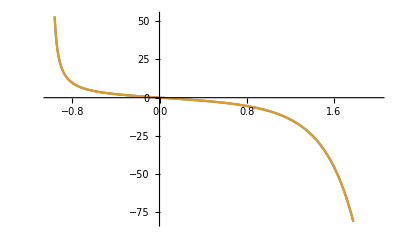

```mathematica
Plot[Evaluate[{c[α,Λ,Ω],-π Ω^α Tan[(π α)/2]-Λ^α(Ω Gamma[1/2 (-1+α)])/Λ}/.Ω-> 1/.Λ->100],{α,-1,2}]
```

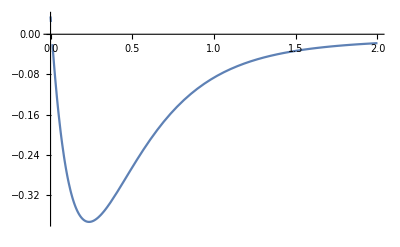

```mathematica
Plot[ Λ^-α c[α,Λ,Ω]/.Ω-> 1/.Λ->100,{α,0,2}]
```

##### Numeric check

```mathematica
NIntegrate[Λ^(1+α)Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 s^2 Λ^2]Sin[Ω s]/.Ω->1/.α->0.1/.Λ->100,{s,0,1000}]
c[α,Λ,Ω]/.Ω->1/.α->0.1/.Λ->100//N
```

-0.44053

-0.440614-3.60327×10^-15 ⅈ

### Spectral distribution and spectral density

μ̃(z)=FT [μ(t)]
∫_(-∞)^∞ ⅇ^(-ⅈ t z) z/(z^2-ω^2)ⅆz=ⅈ π Cos[t ω] - 2 ⅈ π 

∫_0^π ⅇ^(-ⅈ t R ⅇ^(ⅈ θ)) (R ⅇ^(ⅈ θ))/((R ⅇ^(ⅈ θ))^2-ω^2)R ⅇ^(ⅈ θ) ⅈ ⅆθ
	=∫_0^π ⅇ^(-ⅈ t R ⅇ^(ⅈ θ))  ⅈ ⅆθ ,    (R>>1)
	=ⅈ 2 π +  Cos[t R] + O[1/R]
-Graphics-

```mathematica
Integrate[Exp[-ⅈ t R Exp[ⅈ θ]],{θ,0,π}]
```

ⅈ (ExpIntegralEi[-ⅈ R t]-ExpIntegralEi[ⅈ R t])

```mathematica
Series[ⅈ (ExpIntegralEi[-ⅈ R t]-ExpIntegralEi[ⅈ R t]),{R, ∞,0}]//FullSimplify
```

ⅈ (Log[-ⅈ/t]-Log[ⅈ/t]+Log[-ⅈ t]-Log[ⅈ t])+(ⅇ^(-ⅈ t R+O[1/R]^2)+ⅇ^(ⅈ t R+O[1/R]^2)) O[1/R]^1

```mathematica
Residue[z/(z^2-ω^2)ⅇ^(-ⅈ t z),{z,ω}]+Residue[z/(z^2-ω^2)ⅇ^(-ⅈ t z),{z,-ω}]//FullSimplify
```

Cos[t ω]

```mathematica
Integrate[z/(z^2-1),{z,-∞,∞}]
```

Integrate::idiv: Integral of z/(-1+z^2) does not converge on {-∞,∞}.

∫_(-∞)^∞ z/(-1+z^2)ⅆz

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.01363}. NIntegrate obtained 7.35443 and 1.69178 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand z/(z^2-1) is being considered as zero over the specified region, but may actually be divergent.

0.

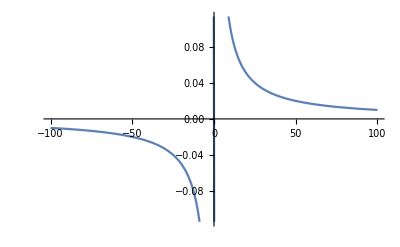

```mathematica
NIntegrate[z/(z^2-1),{z,-1000,1000}]
Plot[z/(z^2-1),{z,-100,100}]
```

## Nonlinear QBM

### From the paper

Particle:
-Graphics-
Harmonic oscillator bath:
-Graphics-
Interaction:
-Graphics-
	Linear coupling: k=1, f(x)=x
	Quadratic coupling: k=2
	Cubic coupling: k=3
	Quartic coupling: k=4

#### Initial bath in thermal eq

-Graphics-
Hence the influence potential factorizes:
-Graphics-

#### Perturbation theory, up to λ^2

F_n[x,x']=Exp{ⅈ/ħ δA_n[x,x']}
The influence action in small λ perturbation:
-Graphics-
where ⟨...⟩_0 is averaging over the bath action, without interaction.

#### Quadratic case k=2

Vertex function
-Graphics-
Renormalized potential
-Graphics- 
-Graphics-

#### Anharmonic case

-Graphics-
Counterterm:
-Graphics-

-Graphics-

-Graphics-
Typo: (∂ f(x'))/(∂ x')ẋ' 
Use standard approach analogous of deriving the wave function from the path integral (see also derivation in Caldeira-Leggett, page 605-607 ), we get: 

-Graphics-

-Graphics-
-Graphics-

Wigner function definition
-Graphics-
Wigner eq for the anharmonic case:
-Graphics-

```mathematica
Integrate[Exp[-a ξ^2+b ξ]ξ,{ξ,-∞,∞}]
```

ConditionalExpression[(b ⅇ^(b^2/(4 a)) √π)/(2 a^(3/2)), Re[a]>0]

#### Semiclassical limit and FP for the anharmonic case

At the semiclassical limit, Wigner eq -> FP eq, 
∂/(∂ t)W = {V_ren,W}+2 γ_o X∂/(∂ p)(X p W)+2 k_B T γ_0 X^2∂^2/(∂ p^2)W
and the asymptotic solution is:
-Graphics-

{V_ren, W} =(∂ V_ren)/(∂ x)(∂ W)/(∂ p)-(∂ V_ren)/(∂ p) (∂ W)/(∂ x)
∂/(∂ p)(X p W)=X W+X p∂/(∂ p)W

∂/(∂ t)W(X,p,t)={ -(∂ V_ren)/(∂ p) ∂/(∂ X)+(∂ V_ren)/(∂ X)∂/(∂ p)+2 γ_o X^2∂/(∂ p)[p ·] +2 k_B T γ_0 X^2∂^2/(∂ p^2)}W(X,p,t)
I think V_ren(X)...

Compare with the one from the classical Brownian motion:
-Graphics-

### Fluctuation Dissipation Relation: ν̂(ω)=-ⅈ η̂(ω)z(ω)

#### Preliminaries

FT Cos[a x] = ∫_(-∞)^∞ Cos[a x] Exp[-i k x]ⅆx =π (δ(k-a)+δ(k+a))
FT Sin[a x] = ∫_(-∞)^∞ Sin[a x] Exp[-i k x]ⅆx =-ⅈ π (δ(k-a)-δ(k+a))

-Graphics-

z(ω)=Coth (β ω)/2
z(-ω)=-z(ω)

```mathematica
z[ω_]:=Coth[β ω /2]
Coth[-x]==-Coth[x]//Simplify
```

True

#### Linear coupling: (ν̂)^(1)(ω)=-ⅈ (η̂)^(1)(ω)z(ω)=z(ω)ω (γ̂)^(1)(ω)

Coupling factors seem to be missing
-Graphics-

I^(1)(ω)=Σ_n 1/(2 m_n ω_n)δ(ω-ω_n)

η^(1)(t)=-∫dω' I^(1)(ω') sin ω' t 
ν^(1)(t)=∫dω' I^(1)(ω') z(ω')cosω' t
γ^(1)(t)=∫dt η^(1)(t)+C=∫dω' (I^(1)(ω'))/ω' cos ω' t+C

(η̂)^(1)(ω)=ⅈ π∫dω' I^(1)(ω')(δ(ω-ω')-δ(ω+ω'))
	=ⅈ π{ I^(1)(ω)-I^(1)(-ω)} 

(γ̂)^(1)(ω)=π/ω {I^(1)(ω)-I^(1)(-ω)}+2π C δ(ω)
	set C=0

(ν̂)^(1)(ω)=π∫dω' I^(1)(ω') z(ω')(δ(ω-ω')+δ(ω+ω'))
	=π I^(1)(ω) z(ω)-π I^(1)(-ω) z(ω)
	=π {I^(1)(ω)-I^(1)(-ω)}z(ω)
	=-ⅈ (η̂)^(1)(ω)z(ω)
	=(γ̂)^(1)(ω) ω z(ω)

#### Quadratic coupling: (ν̂)_0(ω)=z[ω] ω (γ̂)_0(ω)

-Graphics-

I^(2)(ω)=Σ_n C_n^2/(2 m_n ω_n)^2 z(ω_n)δ(ω-ω_n)

η^(2)(t)=-2∫_0^∞ dω' I^(2)(ω') sin(2ω' t)
	=-∫_0^∞ dω' I^(2)(ω'/2) sin(ω' t)
γ^(2)(t)=∫dt η^(2)(t)+C=∫_0^∞ dω' (I^(2)(ω'/2))/ω' cos ω' t+C
ν^(2)(t)=∫_0^∞ dω' I^(2)(ω'){(z(ω')^2+1)/(z(ω'))cos(2ω' t)+(z(ω')^2-1)/(z(ω'))}
	=2∫_0^∞ dω' I^(2)(ω'){Coth[β ω']cos(2ω' t)+Csch[β ω']}
	=∫_0^∞ dω'I^(2)(ω'/2){z(ω') cos(ω' t)+Csch[β ω'/2]}


(η̂)^(2)(ω)=ⅈ π { I^(2)(ω/2)-I^(2)(-ω/2)} 
(γ̂)^(2)(ω)=π/ω {I^(2)(ω/2)-I^(2)(-ω/2)}+2π C δ(ω)
	C=∫dω' I^(2)(ω'/2)Csch[β ω'/2]

(ν̂)^(2)(ω)=-ⅈ (η̂)^(2)(ω)z(ω)+C δ(ω)?

```mathematica
(*γ(t)*) Integrate[-2I2[w]Sin[2 w t],t]d[w]/.w->w/2/.d[w/2]->d[w]/2
(*γ̂(ω)*)%/d[w]/.Cos[x_ t]->δ[x-ω]/.w->ω/.δ[0]->1
(*ν(t)*){ I2[w](z[w]^2+1)/z[w] Cos[2 w t],I2[w](z[w]^2-1)/z[w]}d[w]/.w->w/2/.d[w/2]->d[w]/2//TrigToExp//FullSimplify
(*ν̂(ω)*){%[[1]]/.Cos[x_ t]->δ[x-ω]/.w->ω/.δ[0]->1,%[[2]]δ[ω]}
```

(Cos[t w] d[w] I2[w/2])/w

I2[ω/2]/ω

{Cos[t w] Coth[(w β)/2] d[w] I2[w/2],Csch[(w β)/2] d[w] I2[w/2]}

{Coth[(β ω)/2] d[ω] I2[ω/2],Csch[(w β)/2] d[w] I2[w/2] δ[ω]}

(γ̂)_0(ω)=1/ω I2[ω/2]
(ν̂)_0(ω)=Coth[(β ω)/2] I2[ω/2]=z[ω] ω (γ̂)_0(ω)  

(ν̂)_1(ω)=1/4 δ[ω] ∫dw Csch[(w β)/2] d[w] I2[w/2]

#### Cubic coupling: (ν̂)_0(ω)=z[3ω]9ω(γ̂)_0(3ω)

-Graphics-

I^(3)(ω)=Σ_n(3 ℏ λ^2 C_n^2)/(2(2 m_n ω_n)^3)δ(ω-ω_n) (3 z^2+1)

```mathematica
(*η(t)*)-I3[w]/(3(z [ω])^2+1){9 z[w]^2-3,3(z [ω])^2+1}//TrigToExp//FullSimplify
(*γ(t)*) Integrate[{%[[1]]Sin[w t],%[[2]]Sin[3 w t]},t]d[w]/.w->w/3/.d[w/3]->d[w]/3//Simplify
(*γ̂(ω)*){%[[1]]/.Cos[(t w)/3]->δ[w/3-ω]/.w->3ω/.δ[0]->1/.d[3ω]->3d[ω],%[[2]]/.Cos[t w]->δ[w-ω]/.w->ω/.δ[0]->1}/d[ω]//FullSimplify
Series[%,{β,0,0}]
γT=Plus@@%//Normal
```

{-(3 (2+Cosh[w β]) Csch[(w β)/2]^2 I3[w] Sinh[(β ω)/2]^2)/(1+2 Cosh[β ω]),-I3[w]}

{(3 Cos[(t w)/3] (2+Cosh[(w β)/3]) Csch[(w β)/6]^2 d[w] I3[w/3] Sinh[(β ω)/2]^2)/(w+2 w Cosh[β ω]),(Cos[t w] d[w] I3[w/3])/(3 w)}

{(3 (2+Cosh[β ω]) I3[ω])/(ω+2 ω Cosh[β ω]),I3[ω/3]/(3 ω)}

{(3 I3[ω])/ω+O[β]^1,I3[ω/3]/(3 ω)}

I3[ω/3]/(3 ω)+(3 I3[ω])/ω

```mathematica
Series[(3 (2+Cosh[β ω]))/(ω+2 ω Cosh[β ω]),{ω,0,1}]
```

3/ω-(β^2 ω)/2+O[ω]^2

```mathematica
(*ν(t)*)I3[w]/(3(z [ω])^2+1)z[ω]{ ((z [ω])^2+3)Cos[t w] ,(9(z [ω])^2-3)Cos[3t w] }d[w]/.w->w/3/.d[w/3]->d[w]/3//TrigToExp//FullSimplify
(*ν̂(ω)*) {%[[1]]/. Cos[(t w)/3]->δ[w/3-ω]/.w->3ω/.δ[0]->1/.d[3 ω]->3d[ω],
%[[2]]/.Cos[w t]->δ[w-ω]/.w->ω/.δ[0]->1}/d[ω]
Series[%,{β,0,0}]
νT=Plus@@%//Normal//Simplify
```

{1/3 Cos[(t w)/3] Coth[(3 β ω)/2] d[w] I3[w/3],Cos[t w] Cosh[(β ω)/2] (2+Cosh[β ω]) Csch[(3 β ω)/2] d[w] I3[w/3]}

{Coth[(3 β ω)/2] I3[ω],Cosh[(β ω)/2] (2+Cosh[β ω]) Csch[(3 β ω)/2] I3[ω/3]}

{(2 I3[ω])/(3 ω β)+O[β]^1,(2 I3[ω/3])/(ω β)+O[β]^1}

(2 (3 I3[ω/3]+I3[ω]))/(3 β ω)

```mathematica
νT/γT//FullSimplify
%/.I3[ω/3]->α I3[ω]//Simplify
```

(6 I3[ω/3]+2 I3[ω])/(β I3[ω/3]+9 β I3[ω])

(2+6 α)/(9 β+α β)

```mathematica
Solve[2+6 α==9 +α ,α]
```

{{α→7/5}}

(γ̂)_0(ω)=1/(3 ω) I3[ω/3] ->(γ̂)_0(3ω)=1/(9 ω) I3[ω]
(ν̂)_0(ω)= Coth[(3 β ω)/2] I3[ω]=z[3ω]9ω(γ̂)_0(3ω)

#### Quartic coupling: (ν̂)_0(ω)=z[4ω] ω (γ̂)_0(ω)

-Graphics-

```mathematica
(*η(t)*)-2/((z [ω])^2+1)I4[w]{(2 z[w]^2-1),1/2((z [ω])^2+1)}//TrigToExp//FullSimplify
(*γ(t)*) Integrate[{%[[1]]Sin[2 w t],%[[2]]Sin[4 w t]},t]d[w]/.w->w/4/.d[w/4]->d[w]/4//Simplify
(*γ̂(ω)*){%[[1]]/.Cos[(t w)/2]->δ[w/2-ω]/.w->2ω/.δ[0]->1 /.d[2 ω]->2d[ω],%[[2]]/.Cos[t w]->δ[w-ω]/.w->ω/.δ[0]->1}/d[ω]
Series[%,{β,0,0}]
γT4=Plus@@%//Normal//Simplify
```

{-((3+Cosh[w β]) Csch[(w β)/2]^2 I4[w] Sech[β ω] Sinh[(β ω)/2]^2),-I4[w]}

{(Cos[(t w)/2] (3+Cosh[(w β)/4]) Csch[(w β)/8]^2 d[w] I4[w/4] Sech[β ω] Sinh[(β ω)/2]^2)/(2 w),(Cos[t w] d[w] I4[w/4])/(4 w)}

{((3+Cosh[(β ω)/2]) Csch[(β ω)/4]^2 I4[ω/2] Sech[β ω] Sinh[(β ω)/2]^2)/(2 ω),I4[ω/4]/(4 ω)}

{(8 I4[ω/2])/ω+O[β]^1,I4[ω/4]/(4 ω)}

(I4[ω/4]+32 I4[ω/2])/(4 ω)

```mathematica
(*ν(t)*)2/((z [ω])^2+1)I4[w]/z[ω]{1/8(7 z[ω]^4-10(z [ω])^2+3), 1/2(3 z[ω]^4+(z [ω])^2-2)Cos[2t w] ,1/8(z[ω]^4+6(z [ω])^2+1)Cos[4t w] }d[w]/.w->w/4/.d[w/4]->d[w]/4//TrigToExp//FullSimplify
(*ν̂(ω)*) {%[[1]]δ[ω],%[[2]]/. Cos[(t w)/2]->δ[w/2-ω]/.w->2ω/.δ[0]->1/.d[2 ω]->2d[ω]/d[ω],
%[[3]]/.Cos[w t]->δ[w-ω]/.w->ω/.δ[0]->1/d[ω]}
Series[%,{β,0,0}]
νT4=Plus@@%//Normal//Simplify
```

{1/4 (5+2 Cosh[β ω]) Csch[2 β ω] d[w] I4[w/4],1/4 Cos[(t w)/2] (5+Cosh[β ω]) Csch[β ω] d[w] I4[w/4],1/4 Cos[t w] Coth[2 β ω] d[w] I4[w/4]}

{1/4 (5+2 Cosh[β ω]) Csch[2 β ω] d[w] I4[w/4] δ[ω],1/2 (5+Cosh[β ω]) Csch[β ω] I4[ω/2],1/4 Coth[2 β ω] I4[ω/4]}

{(7 d[w] I4[w/4] δ[ω])/(8 ω β)+O[β]^1,(3 I4[ω/2])/(ω β)+O[β]^1,I4[ω/4]/(8 ω β)+O[β]^1}

(I4[ω/4]+24 I4[ω/2]+7 d[w] I4[w/4] δ[ω])/(8 β ω)

```mathematica
νT4/γT4/.d[w]->0//FullSimplify
```

(I4[ω/4]+24 I4[ω/2])/(2 β I4[ω/4]+64 β I4[ω/2])

(γ̂)_0(ω)=1/(4 ω) I4[ω/4]
(ν̂)_0(ω)=1/4 Coth[2 β ω] I4[ω/4]=Coth[2 β ω]  ω (γ̂)_0(ω)  

(γ̂)_1(ω)=1/(2 ω)I4[ω/2] (3+Cosh[(β ω)/2]) Csch[(β ω)/4]^2 Sech[β ω] Sinh[(β ω)/2]^2
(ν̂)_1(ω)=1/4 (5+16 Cosh[β ω]+3 Cosh[2 β ω]) Csch[2 β ω] I4[ω/2]
(ν̂)_2(ω)=1/4 δ[ω] ∫dw (5+2 Cosh[β ω]) Csch[2 β ω] d[w] I4[w/4]

## Quantum Langevin

### Inverse Laplace

[Laplace notes](http://www.eng.uwaterloo.ca/~jzelek/teaching/syde252/Laplace-roc.pdf)

Bilateral Laplace vs unilateral:
G^=(s)=∫_(-∞)^∞ ⅆt  ⅇ^(-s t) G(t)=∫_0^∞ ⅆt  ⅇ^(-s t) G(t)=Ĝ(s)
	only if G(t)∝u(t)
	u(t) is the unit step

Bilateral Laplace is related to Fourier:
	 F^=(s)≡∫_(-∞)^∞ ⅆt  ⅇ^(-s t) F(t)
{s=σ+ⅈω ∈ROC}
	=∫_(-∞)^∞ ⅆt  ⅇ^(-ⅈ ω t) ⅇ^(-σ t) F(t) 
Inverse Fourier both sides with a fixed σ ∈ ROC:
	ⅇ^(-σ t)F(t)=1/(2 π)∫_(-∞)^∞ ⅆω  ⅇ^(ⅈ ω t) F^=(σ+ⅈω)
	{s=σ+ⅈω , ds=ⅈ dω}
		=1/(2 π ⅈ)∫_(σ-ⅈ∞)^(σ+ⅈ∞) ⅆs  ⅇ^(-σ t)ⅇ^(s t) F^=(s)
F(t)=1/(2 π ⅈ)∫_(σ-ⅈ∞)^(σ+ⅈ∞) ⅆs  ⅇ^(s t) F^=(s)

If σ=0:F(t)=1/(2 π)∫_(-∞)^∞ ⅆω  ⅇ^(ⅈ ω t) F^=(ⅈω)
	F̃(ω)=F^=(ⅈω)

### Laplace transform

L{x^(..)(t)}(s)=∫_0^∞ Exp[-st] x^(..)(t)ⅆt
		=∫_0^∞ d/dt{Exp[-st] ẋ(t)}ⅆt+s∫_0^∞ Exp[-st] ẋ(t)ⅆt
		=- ẋ(0)+s ∫_0^∞ d/dt{Exp[-st] x(t)}ⅆt+s^2∫_0^∞ Exp[-st] x(t)ⅆt
		=- ẋ(0)-s x(0)+s^2 x̂(s) 

L{γ*ẋ}(s)=γ̂(s)∫_0^∞ Exp[-st] ẋ(t)ⅆt
		=γ̂(s) (-x(0)+s x̂(s) )

x̂(s)≡L{x(t)}(s)

#### Laplace transform of convolution: L{f*g}=f̂ ĝ

[Laplace convolution](https://ocw.mit.edu/courses/mathematics/18-03sc-differential-equations-fall-2011/unit-iii-fourier-series-and-laplace-transform/transfer-system-and-weight-functions-greens-formula/MIT18_03SCF11_s30_5text.pdf)

### Correlation functions

x(t)=∫_0^t G(t-s) F(s)ⅆs

⟨x(t)x(t')⟩=⟨∫_0^t G(t-s) F(s)ⅆs ∫_0^t' G(t'-s') F(s')ⅆs'⟩
		=∫_0^t ⅆs G(t-s) ∫_0^t' ⅆs'G(t'-s') ⟨F(s)F(s')⟩
		=∫_0^t ⅆs G(t-s) ∫_0^t' ⅆs'G(t'-s') ν(s-s')
⟨(x(t))^2⟩=∫_0^t ⅆs ∫_0^t ⅆs'G(t-s) G(t-s') ν(s-s')

⟨[x-x_0]^2⟩=⟨x^2⟩-2⟨ x ⟩x_0+x_0^2

```mathematica
Expand@((x-x0)^2)
```

x^2-2 x x0+x0^2

```mathematica
Solve[xs==1/2(x1+x2)&&xa==x1-x2,{x1,x2}]
```

{{x1→1/2 (xa+2 xs),x2→1/2 (-xa+2 xs)}}

### Pure Ohmic case

#### Free particle case

```mathematica
(2π ⅈ)/(-2π M)(Residue[Exp[ⅈ ω t] 1/((ω-ⅈ ϵ) (ω-ⅈ 2γ0)),{ω,ⅈ ϵ}]+Residue[Exp[ⅈ ω t] 1/(ω^2-ⅈ 2γ0 ω),{ω,ⅈ 2 γ0}])//Simplify
%/. 1/(-2γ0+ϵ)-> 1/(-2γ0)//Simplify
```

-(ⅇ^(-2 t γ0)/γ0+(2 ⅇ^(-t ϵ))/(-2 γ0+ϵ))/(2 M)

-(ⅇ^(-2 t γ0)-ⅇ^(-t ϵ))/(2 M γ0)

#### Harmonic oscillator: G(t)=(ⅇ^(-t γ) Sinh[t √(γ^2-Ω^2)])/(√(γ^2-Ω^2))u(t), γ>Ω G(t)=(ⅇ^(-t γ) Sin[t √(-γ^2+Ω^2)])/(√(-γ^2+Ω^2))u(t), γ<Ω

G̃(ω)=1/(-ω^2+ⅈ 2 γ ω+Ω^2)

##### Laplace

For Ohmic case:
	F^=(s)=1/(s^2+2 s γ+Ω^2)
Poles are on the left half plane, hence we can use Fourier instead.
	F(t)=1/(2 π)∫_(-∞)^∞ ⅆω  ⅇ^(ⅈ ω t) F^=(ⅈω)

```mathematica
-w^2+ⅈ 2 γ w+Ω^2/.w->-ⅈ s
Assuming[γ>0&&Ω>0&&γ>Ω,Solve[%==0,s]] (* poles on the left half plane*)
Assuming[γ>0&&Ω>0&&γ<Ω,Solve[%%==0,s]] (* poles on the left half plane*)
```

s^2+2 s γ+Ω^2

{{s→ConditionalExpression[-γ-√(γ^2-Ω^2)-ⅈ √(Ω^2+2 γ (-γ-√(γ^2-Ω^2))+(-γ-√(γ^2-Ω^2))^2), γ>Ω]},{s→ConditionalExpression[-γ+√(γ^2-Ω^2)-ⅈ √(Ω^2+2 γ (-γ+√(γ^2-Ω^2))+(-γ+√(γ^2-Ω^2))^2), γ>Ω]}}

{{s→ConditionalExpression[-γ-ⅈ √(-γ^2+Ω^2), γ<Ω]},{s→ConditionalExpression[-γ+ⅈ √(-γ^2+Ω^2), γ<Ω]}}

##### Solution

F(t)=1/(2 π)∫_(-∞)^∞ ⅆω  ⅇ^(ⅈ ω t) F^=(ⅈω)
	=1/(2 π)2π ⅈ Sum of residues
Poles are on the upper half plane of the ω-plane.  
	For t>0, we close the contour in the upper half plane  in order for the arc contribution to vanish.
	For t<0, we close the contour in the lower half plane and since there are no poles, the integral is zero.
Solution for 2 cases:
	G(t)=(ⅇ^(-t γ) Sinh[t √(γ^2-Ω^2)])/(√(γ^2-Ω^2))u(t), γ>Ω  
G(t)=(ⅇ^(-t γ) Sin[t √(-γ^2+Ω^2)])/(√(-γ^2+Ω^2))u(t), γ<Ω

```mathematica
-w^2+ⅈ 2 γ w+Ω^2==0
Assuming[γ>0&&Ω>0&&γ>Ω,Solve[%,w]]
Assuming[γ>0&&Ω>0&&γ<Ω,Solve[%%,w]]
```

-w^2+2 ⅈ w γ+Ω^2==0

{{w→ConditionalExpression[ⅈ (γ-√(γ^2-Ω^2)), γ>Ω]},{w→ConditionalExpression[ⅈ (γ+√(γ^2-Ω^2)), γ>Ω]}}

{{w→ConditionalExpression[ⅈ γ-√(-γ^2+Ω^2), γ<Ω]},{w→ConditionalExpression[ⅈ γ+√(-γ^2+Ω^2), γ<Ω]}}

(ⅇ^(-t γ) Sinh[t √(γ^2-Ω^2)])/(√(γ^2-Ω^2))

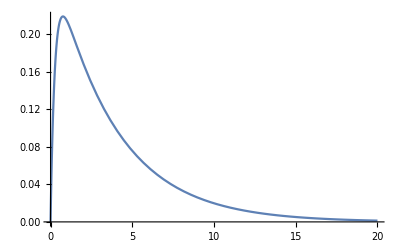

```mathematica
Assuming[γ>0&&Ω>0&&γ>Ω,(2π ⅈ)/(2π)(Residue[Exp[ⅈ ω t]/(-ω^2+ⅈ 2γ ω+Ω^2),{ω,ⅈ (γ-√(γ^2-Ω^2))}]+Residue[Exp[ⅈ ω t]/(-ω^2+ⅈ 2γ ω+Ω^2),{ω,ⅈ (γ+√(γ^2-Ω^2))}])//FullSimplify]//Simplify
Plot[%/.γ->2/.Ω->1,{t,0,20}]
```

(ⅇ^(-t γ) Sin[t √(-γ^2+Ω^2)])/(√(-γ^2+Ω^2))

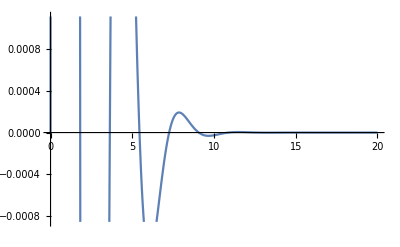

```mathematica
Assuming[γ>0&&Ω>0&&γ<Ω,(2π ⅈ)/(2π)(Residue[Exp[ⅈ ω t]/(-ω^2+ⅈ 2γ ω+Ω^2),{ω,ⅈ γ-√(-γ^2+Ω^2)}]+Residue[Exp[ⅈ ω t]/(-ω^2+ⅈ 2γ ω+Ω^2),{ω,ⅈ γ+√(-γ^2+Ω^2)}])//FullSimplify]//Simplify
Plot[%/.γ->1/.Ω->2,{t,0,20}]
```

```mathematica
Series[γ- √(γ^2-Ω^2),{Ω,0,2}]
```

(γ-√(γ^2))+Ω^2/(2 √(γ^2))+O[Ω]^3

### Subohmic case

#### Laplace

F^=(s)=1/(s^2+ γ √s+Ω^2)
2 poles: s_±=-a+±ⅈ b, where  a,b>0

```mathematica
ComplexPlot[s^2+γ √s+Ω^2/.γ->1/.Ω->6,{s,-10I-10, 10I+10}]
```

-Graphics-

```mathematica
z^4+ γ z+Ω^2;
Solve[%==0,z]//FullSimplify;
z^2/.%/.γ->1/.Ω->6//N
```

{-0.144317-6.14436 ⅈ,-0.144317+6.14436 ⅈ,0.144317+5.85564 ⅈ,0.144317-5.85564 ⅈ}

```mathematica
{{s->-0.14431669870941774+6.144357458381141 ⅈ},{s->-0.14431669870934877-6.144357458381025 ⅈ},{s->0.14431669870934388-5.855640532229604 ⅈ},{s->0.1443166987094226+5.855640532229487 ⅈ}}
```

```mathematica
s^2+ γ √s+Ω^2;
Solve[%==0,s]//FullSimplify(* poles on the left half plane*)
%/.γ->1/.Ω->6//N
```

{{s→1/6 (-√3 √(-4 Ω^2+(16 Ω^4)/(((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))-3 √(-(8 Ω^2)/3-(16 Ω^4)/(3 ((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))-1/3 ((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3)-(2 √6 γ^2)/(√(-8 Ω^2+(32 Ω^4)/(((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+2^(2/3) (27 γ^4-128 Ω^6+3 √(81 γ^8-768 γ^4 Ω^6))^(1/3)))))},{s→1/6 (-√3 √(-4 Ω^2+(16 Ω^4)/(((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+3 √(-(8 Ω^2)/3-(16 Ω^4)/(3 ((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))-1/3 ((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3)-(2 √6 γ^2)/(√(-8 Ω^2+(32 Ω^4)/(((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+2^(2/3) (27 γ^4-128 Ω^6+3 √(81 γ^8-768 γ^4 Ω^6))^(1/3)))))},{s→1/6 (√3 √(-4 Ω^2+(16 Ω^4)/(((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))-3 √(-(8 Ω^2)/3-(16 Ω^4)/(3 ((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))-1/3 ((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3)+(2 √6 γ^2)/(√(-8 Ω^2+(32 Ω^4)/(((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+2^(2/3) (27 γ^4-128 Ω^6+3 √(81 γ^8-768 γ^4 Ω^6))^(1/3)))))},{s→1/6 (√3 √(-4 Ω^2+(16 Ω^4)/(((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+3 √(-(8 Ω^2)/3-(16 Ω^4)/(3 ((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))-1/3 ((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3)+(2 √6 γ^2)/(√(-8 Ω^2+(32 Ω^4)/(((27 γ^4)/2-64 Ω^6+3/2 √(81 γ^8-768 γ^4 Ω^6))^(1/3))+2^(2/3) (27 γ^4-128 Ω^6+3 √(81 γ^8-768 γ^4 Ω^6))^(1/3)))))}}

{{s→-0.144317+6.14436 ⅈ},{s→-0.144317-6.14436 ⅈ},{s→0.144317-5.85564 ⅈ},{s→0.144317+5.85564 ⅈ}}

#### Fourier

```mathematica
iG=γ √(ⅈ ω)-ω^2+Ω^2/.γ->1/.Ω->6
poles=Solve[%==0,ω]//N
```

36+√(ⅈ ω)-ω^2

{{ω→-6.14436+0.144317 ⅈ},{ω→6.14436+0.144317 ⅈ}}

```mathematica
Exp[ⅈ ω t]/(ω-ω/.poles[[2]])
```

ComplexInfinity

```mathematica
Residue[Exp[ⅈ ω t]/(ω-(ω/.poles[[2]])),{ω,poles[[1]]}]
```

Residue[ⅇ^(ⅈ t ω)/((-6.14436-0.144317 ⅈ)+ω),{ω,{ω→-6.14436+0.144317 ⅈ}}]

```mathematica
(Exp[ⅈ ω t]/(ω-(ω/.poles[[2]]))/.poles[[1]])+(Exp[ⅈ ω t]/(ω-(ω/.poles[[1]]))/.poles[[2]])//FullSimplify//Chop
```

-0.0813755 ⅇ^((-0.144317-6.14436 ⅈ) t)+0.0813755 ⅇ^((-0.144317+6.14436 ⅈ) t)

```mathematica
s^2+γ √s+Ω^2/.s->ⅈ ω
ComplexPlot[%/.γ->1/.Ω->6,{ω,-10I-10, 10I+10}]
```

γ √(ⅈ ω)-ω^2+Ω^2

-Graphics-

```mathematica
ⅈ(1/(b^2+Ω^2-ⅈ γ √b)-0/(b^2+Ω^2+ⅈ γ √b))Exp[-b t]//FullSimplify
Integrate[%,{b,0,∞}]
```

(ⅈ ⅇ^(-b t))/(b^2-ⅈ √b γ+Ω^2)

∫_0^∞ (ⅈ ⅇ^(-b t))/(b^2-ⅈ √b γ+Ω^2)ⅆb

```mathematica
param=FindFit[Transpose@{Range[1,100,1],int},a t^(-3/2),{a},t]
```

{a→-0.00120028}

```mathematica
ⅈ(1/(b^2+Ω^2-ⅈ γ √b)-1/(b^2+Ω^2+ⅈ γ √b))Exp[-b t]/.γ->1/.Ω->6//Simplify
int=NIntegrate[%/.t->Range[1,100,1],{b,0,∞}];
```

-(2 √b ⅇ^(-b t))/(1296+b+72 b^2+b^4)

```mathematica
Integrate[-(2 √b ⅇ^(-b t))/1296,{b,0,∞}]
%//N
```

ConditionalExpression[-(√π)/(1296 t^(3/2)), Re[t]>0]

ConditionalExpression[-0.00136763/t^(3/2), Re[t]>0.]

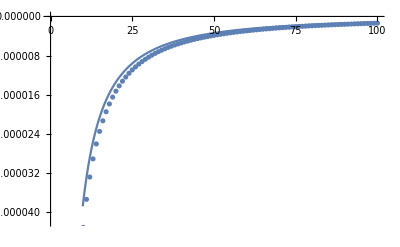

```mathematica
Show[ListPlot@Transpose@{Range[1,100,1],int},Plot[a t^(-3/2)/.param,{t,0,100}]]
```

## Other investigations

### Green’s functions

Δ(t,t'):=⟨[x(t),x'(t')]⟩
G_R(t,t'):=ⅈ θ(t-t') Δ(t,t')
G_S(t,t'):=1/2⟨{x(t),x'(t')}⟩

G_(s a)(t,t'):=-ⅈ ⟨x_s(t)x_a(t')⟩
G_(s s)(t,t'):=-ⅈ ⟨x_s(t)x_s(t')⟩
G_(a a)(t,t'):=-ⅈ ⟨x_a(t)x_a(t')⟩=0

G_S(t,t')=G_(s s)(t,t')
G_R(t,t')=G_(s a)(t,t')
G_A(t,t')=G_(a s)(t,t')
G_R(t,t')=G_A(t',t)


G^T(t,t')=θ(t-t') G^>(t,t')+θ(t'-t) G^<(t,t')

[x(t),x'(t')]=1/4 [2x_s(t)+x_a(t),2x_s(t')-x_a(t')]
	                =[x_s(t),x_s(t')]-1/2 [x_s(t),x_a(t')]-1/2 [x_s(t'),x_a(t)]-1/4 [x_a(t),x_a(t')]

	[x_s(t),x_a(t')]-[x_s(t'),x_a(t)]
		=x_s(t)x_a(t')-x_a(t')x_s(t)-x_s(t')x_a(t)+x_a(t)x_s(t')
		-> G_(s a)(t,t')-G_(a s)(t',t)-G_(s a)(t',t)+G_(a s)(t,t')
			=G_R(t,t')-G_A(t',t)-G_R(t',t)+G_A(t,t')
			=G_R(t,t')-G_R(t,t')-G_R(t',t)+G_R(t',t)
			=0
Δ(t,t')=⟨[x(t),x'(t')]⟩
	    =⟨x_s(t)x_s(t')⟩-⟨x_s(t')x_s(t)⟩-1/4 ⟨x_a(t)x_a(t')⟩+1/4 ⟨x_a(t')x_a(t)⟩

{x(t),x'(t')}={x_s(t),x_s(t')}+1/2 {x_a(t),x_s(t')}-1/2 {x_s(t),x_a(t')}-1/4 {x_a(t),x_a(t')}

 {x_a(t),x_s(t')}-{x_s(t),x_a(t')}
	= x_a(t)x_s(t')+x_s(t')x_a(t)-x_s(t)x_a(t')-x_a(t')x_s(t)
	-> G_(a s)(t,t')+G_(s a)(t',t)-G_(s a)(t,t')-G_(a s)(t',t)
		=G_A(t,t')+G_R(t',t)-G_R(t,t')-G_A(t',t)
		=2G_R(t',t)-2G_R(t,t')
		=-2 Δ(t,t')


G_S(t,t')=1/2⟨{x_s(t),x_s(t')}⟩-1/8 ⟨{x_a(t),x_a(t')}⟩-1/2 Δ(t,t')
	=1/2⟨x_s(t)x_s(t')⟩+1/2⟨x_s(t')x_s(t)⟩-1/8 ⟨x_a(t)x_a(t')⟩-1/8 ⟨x_a(t')x_a(t)⟩-1/2⟨x_s(t)x_s(t')⟩+1/2⟨x_s(t')x_s(t)⟩+1/8 ⟨x_a(t)x_a(t')⟩-1/8 ⟨x_a(t')x_a(t)⟩
	=⟨x_s(t')x_s(t)⟩-1/4 ⟨x_a(t')x_a(t)⟩

```mathematica
({{gpp, gpm}, {gmp, gmm}}).({{jp}, {jm}})//Expand
({{jp, jm}}).%//Expand
```

{{gpm jm+gpp jp},{gmm jm+gmp jp}}

{{gmm jm^2+gmp jm jp+gpm jm jp+gpp jp^2}}

```mathematica
Λ=({{1, 1/2}, {1, -1/2}});
(Inverse@Λ).{J1,J2}
```

{J1/2+J2/2,J1-J2}

```mathematica
Λ=({{1, 1/2}, {1, -1/2}});
Transpose[Λ].({{gT, -glt}, {-ggt, gTi}}).Λ//Simplify//MatrixForm
%/.gT+gTi->ggt+glt//MatrixForm
```

(-ggt-glt+gT+gTi | 1/2 (-ggt+glt+gT-gTi)
1/2 (ggt-glt+gT-gTi) | 1/4 (ggt+glt+gT+gTi))

(0 | 1/2 (-ggt+glt+gT-gTi)
1/2 (ggt-glt+gT-gTi) | 1/4 (2 ggt+2 glt))

### Diffusion corrections

```mathematica
{-(λ(λ+λtilde)+2 λprime DD[0])/2 DD[0],λtildeprime κ[T]}//Expand (*c^2 T^2/D multiplying all the terms*);
{List@@%[[1]],%[[2]]}//Flatten
%/.λ->DD[1]/(c[0] T)/.λtilde->κ[1]/(c[0]^2 T)/.λprime->-(3c[2] DD[0]+8c[1] DD[1]+c[0] DD[2])/(4 c[0]^3 T^2)/.λtildeprime->(κ[2] c[0]- κ[1] c[1])/(2 c[0]^4 T^2)//Simplify
%/.c[0]->c[T]/.c[2]->T^2 D[c[T],{T,2}]/.c[1]->T^1 D[c[T],{T,1}];
%/.DD[0]->DD[T]/.DD[2]->T^2 D[DD[T],{T,2}]/.DD[1]->T^1 D[DD[T],{T,1}];
%/.κ[1]->T^1 D[κ[T],{T,1}]/.κ[2]->T^2 D[κ[T],{T,2}];
%/.c->Function[T,DD[T]](*DD[T]=κ[T]/c[T]*)
```

{-1/2 λ^2 DD[0],-1/2 λ λtilde DD[0],-λprime DD[0]^2,λtildeprime κ[T]}

{-(DD[0] DD[1]^2)/(2 T^2 c[0]^2),-(DD[0] DD[1] κ[1])/(2 T^2 c[0]^3),(DD[0]^2 (3 c[2] DD[0]+8 c[1] DD[1]+c[0] DD[2]))/(4 T^2 c[0]^3),((-c[1] κ[1]+c[0] κ[2]) κ[T])/(2 T^2 c[0]^4)}

{-DD'[T]^2/(2 DD[T]),-(DD'[T] κ'[T])/(2 DD[T]^2),(8 T^2 DD'[T]^2+4 T^2 DD[T] DD''[T])/(4 T^2 DD[T]),(κ[T] (-T^2 DD'[T] κ'[T]+T^2 DD[T] κ''[T]))/(2 T^2 DD[T]^4)}

```mathematica
DD[2]/.DD[i_]->T^i D[κ[T]/c[T],{T,2}]
```

T^2 (-(2 c'[T] κ'[T])/c[T]^2+κ[T] ((2 c'[T]^2)/c[T]^3-c''[T]/c[T]^2)+κ''[T]/c[T])

### Analytic properties of retarded Green’s functions

```mathematica
realIm[z_]:=Module[{zX,re,im},
zX=ComplexExpand[z/.ω->x+ⅈ y];
re=zX-zX[[-1]];
im=zX[[-1]]/ⅈ;
{re,im}]
-ω^2+1+ⅈ ω^-2/.ω->x+ⅈ y//ComplexExpand
realIm[%]
Assuming[Element[x,Reals]&&Element[y,Reals],Solve[%==0,{x,y}]]//N
```

1-x^2+y^2+(2 x y)/((x^2+y^2)^2)+ⅈ (-2 x y+x^2/((x^2+y^2)^2)-y^2/((x^2+y^2)^2))

{1-x^2+y^2+(2 x y)/((x^2+y^2)^2),-2 x y+x^2/((x^2+y^2)^2)-y^2/((x^2+y^2)^2)}

{{x→-0.443262,y→0.704787},{x→0.443262,y→-0.704787},{x→-1.17107,y→-0.266769},{x→1.17107,y→0.266769}}

```mathematica
Solve[-ω^2+Ω^2+ⅈ 2 γ0 ω^1==0,ω]
```

{{ω→ⅈ γ0-√(-γ0^2+Ω^2)},{ω→ⅈ γ0+√(-γ0^2+Ω^2)}}

```mathematica
ComplexPlot[Coth[ω/2],{ω,-4-4 I,4+4 I}]
```

-Graphics-

```mathematica
Solve[s^2+√s+1==0,s]//N
s^2+√s+1/.%//Chop
```

{{s→-0.343815+1.35843 ⅈ},{s→-0.343815-1.35843 ⅈ}}

{0,0}

```mathematica
(-Sin[θ/2])/Sin[2 θ] Cos[2θ]+Cos[θ/2]+1//TrigToExp//FullSimplify//TrigExpand
%/.Sec[θ/2]->1/c/.Sin[θ/2]^2->1-Cos[θ/2]^2/.Cos[θ/2]->c//Simplify
Solve[%==0,c]
```

1+1/4 Sec[θ/2]+Cos[θ/2]/(2 (Cos[θ/2]^2-Sin[θ/2]^2))

1/4 (4+1/c+(2 c)/(-1+2 c^2))

{{c→Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.9009688679024191},{c→Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144},{c→Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587335}}

```mathematica
1/Cos[x]==Sec[x]
```

True

```mathematica
Solve[(-Sin[θ/2])/Sin[2 θ] Cos[2θ]+Cos[θ/2]+1,θ]
```

Solve[1+Cos[θ/2]-Cot[2 θ] Sin[θ/2],θ]

```mathematica
ComplexPlot[s^2+√s+1,{s,-1/2-1.5 I,1/2+2.5 I}]
```

-Graphics-

```mathematica
Integrate[Exp[ⅈ ω t] 1/ω^(3/2),ω]
```

-(2 (ⅇ^(ⅈ t ω)-√(-ⅈ t ω) Gamma[1/2,-ⅈ t ω]))/(√ω)

```mathematica
ⅈ
```

```mathematica
ComplexPlot[s+1+√s/.s->ⅈ ω,{ω,-2-2 I,2+2 I}]
```

-Graphics-

```mathematica
-ω^2+1-ⅈ ω μ/.μ->(-ⅈ ω)^γ/.γ->-1/2
%/.ω->-ⅈ s
Solve[%==0,s]//N
```

1-(ⅈ ω)/(√(-ⅈ ω))-ω^2

1-s/(√-s)+s^2

{{s→0.343815+1.35843 ⅈ},{s→0.343815-1.35843 ⅈ}}

```mathematica
NSolve[0==1+ⅈ √s+s^2,s]
NSolve[0==1-ⅈ √s+s^2,s]
Solve[0==1+√-s+s^2,s]//Simplify
NSolve[0==1-s/(√-s)+s^2,s]
NSolve[0==1+s/(√s)+s^2,s]
NSolve[0==1+√s+s^2,s]
```

{{s→0.343815-1.35843 ⅈ},{s→-0.343815+0.625358 ⅈ}}

{{s→0.343815+1.35843 ⅈ},{s→-0.343815-0.625358 ⅈ}}

{{s→1/2 √(1/3 (-4+16/(1/2 (-101+3 ⅈ √687))^(1/3)+(1/2 (-101+3 ⅈ √687))^(1/3)))-1/2 √(-8/3-16/(3 (1/2 (-101+3 ⅈ √687))^(1/3))-1/3 (1/2 (-101+3 ⅈ √687))^(1/3)-2/(√(1/3 (-4+16/(1/2 (-101+3 ⅈ √687))^(1/3)+(1/2 (-101+3 ⅈ √687))^(1/3)))))},{s→1/2 √(1/3 (-4+16/(1/2 (-101+3 ⅈ √687))^(1/3)+(1/2 (-101+3 ⅈ √687))^(1/3)))+1/2 √(-8/3-16/(3 (1/2 (-101+3 ⅈ √687))^(1/3))-1/3 (1/2 (-101+3 ⅈ √687))^(1/3)-2/(√(1/3 (-4+16/(1/2 (-101+3 ⅈ √687))^(1/3)+(1/2 (-101+3 ⅈ √687))^(1/3)))))}}

{{s→0.343815-1.35843 ⅈ},{s→0.343815+1.35843 ⅈ}}

{{s→-0.343815-1.35843 ⅈ},{s→-0.343815+1.35843 ⅈ}}

{{s→-0.343815-1.35843 ⅈ},{s→-0.343815+1.35843 ⅈ}}

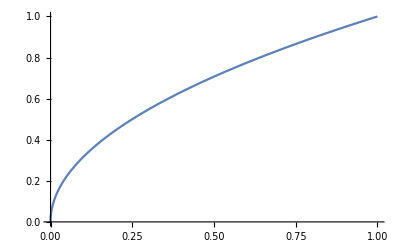

```mathematica
Plot[√x,{x,0,1}]
```

```mathematica
{√(1+ⅈ 2),√(ⅈ(1+ⅈ 2))}//N
```

{1.27202+0.786151 ⅈ,0.343561+1.45535 ⅈ}

```mathematica
ComplexPlot[1/(1+√s+s^2)/.s->ⅈ ω,{ω,-2-2 I,2+2 I}]
```

-Graphics-

```mathematica
ComplexPlot[1/(-ω^2+1-ⅈ ω μ)/.μ->(-ⅈ ω)^γ/.γ->-1/2,{ω,-2-2 I,2+2 I}]
```

-Graphics-

### Sub-ohmic case in Fleming-Roura-Hu

(√(2/π) γ √ω)/(t^(3/2) (γ^2-ω^2)^2)

{(-0.050813-0.123903 ⅈ) 2.71828^((-1.+2.18174 ⅈ) t) Erfc[(-0.83666-1.30384 ⅈ) √t]-(0.050813-0.123903 ⅈ) 2.71828^((-1.-2.18174 ⅈ) t) Erfc[(-0.83666+1.30384 ⅈ) √t]-(0.0888997+0. ⅈ) 2.71828^((0.0834849+0. ⅈ) t) Erfc[(0.288937+0. ⅈ) √t]+(0.190526+0. ⅈ) 2.71828^((1.91652+0. ⅈ) t) Erfc[(1.38438+0. ⅈ) √t],1.02438/t^(3/2)}

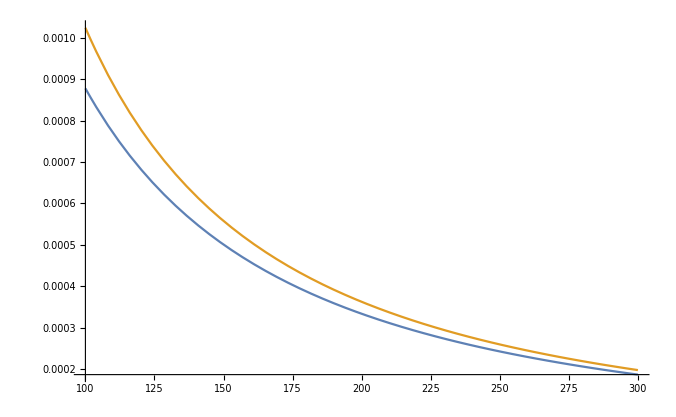

```mathematica
r={1/(√2)(√ω+ⅈ √(ω+2 γ)),1/(√2)(√ω-ⅈ √(ω+2 γ)),1/(√2)(-√ω+ⅈ √(ω-2 γ)),1/(√2)(-√ω-ⅈ √(ω-2 γ))};
A={Product[1/(r[[1]]-r[[i]]),{i,2,4}],1/(r[[2]]-r[[1]])Product[1/(r[[2]]-r[[i]]),{i,3,4}],1/(r[[3]]-r[[4]])Product[1/(r[[3]]-r[[i]]),{i,1,2}],Product[1/(r[[4]]-r[[i]]),{i,1,3}]}//Simplify;
GR=Sum[A[[k]]r[[k]] ⅇ^(r[[k]]^2 t)Erfc[-r[[k]] √t],{k,1,4}];
GRapprox=-1/(√(π t))Sum[A[[k]](1-1/(2 t r[[k]]^2)+0 3/(4 r[[k]]^4 t^2)),{k,1,4}] //Simplify(*(1-0 1/(2 t r[[k]]^2)+0 3/(4 r[[k]]^4 t^2))*)
{GR, GRapprox}/.ω->1.4/.γ->1//N
Plot[%,{t,100,300}]
```

### Ford et al: spectral density odd extension: I(-ω)=-I(ω), ω>0 I(ω)=-I(-ω), ω<0 I(0)=0

I(ω)=ω Re[ γ̃(ω+ⅈ ϵ)]
Example from their paper
	γ̃(ω)=(-ⅈ ω)^γ
	Re[γ̃(±ω)]=(∓ⅈ )^γ ω^γ=ⅇ^(∓ⅈ π/2 γ)ω^γ=Cos(π/2 γ)ω^γ, ω>0
	I(ω)=ω Cos(π/2 γ)ω^γ, ω>0
	I(-ω)=-ω Cos(π/2 γ)ω^γ=-I(ω), ω>0
Example when it's real
	γ̃(ω)=ω^γ
	Re[γ̃(±ω)]=(±1 )^γ ω^γ=ⅇ^(±ⅈ π γ)ω^γ=Cos(π γ)ω^γ
	I(ω)=ω Cos(π γ)ω^γ !=γ̃(ω)
	I(-ω)=-ω Cos(π γ)ω^γ=-I(ω)

### Fourier vs Laplace

#### μ_X[t]=2μ[t]=-∫_(-∞)^∞ dω I[ω] Sin[ω t] μ_(X,+)[t]=2μ_+[t]=-∫_(-∞)^∞ dω I[ω] Sin[ω t]u[t]

μ[t]=-∫_0^∞ dω I[ω] Sin[ω t]
μ_X[t]=-∫_(-∞)^∞ dω I[ω] Sin[ω t]=2μ[t]

Extension to negative ω:  I(-ω)=-I(ω), ω>0
	-∫_(-∞)^0 dω I[ω] Sin[ω t]
			{ω->-ω}
				=∫_0^∞ dω I[-ω] Sin[ω t]
			{I(-ω)=-I(ω), ω>0}
				=-∫_0^∞ dω I[ω] Sin[ω t]=μ[t]

#### Fourier

##### μ̃[ω]=ⅈ π I[|ω|] sgn[ω], with I[0]=0

μ̃[ω]=FT {μ[t]}=-∫_0^∞ dw I[w] FT{Sin[w t]}
			=ⅈ π∫_0^∞ dw I[w]  (δ(ω-w)-δ(ω+w))
			=ⅈ π {I[ω] | ; | ω>0
-I[-ω] | ; | ω<0
0 | ; | ω=0 }
ω=0
	∫_0^∞ dw I[w]δ(-w)= I[0]
	∫_0^∞ dw I[w]δ(w)= I[0]
ω>0
	∫_0^∞ dw I[w]δ(ω-w)= I[ω]
	∫_0^∞ dw I[w]δ(ω+w)= 0
ω<0
	∫_0^∞ dw I[w]δ(ω-w)= 0
	∫_0^∞ dw I[w]δ(ω+w)=  I[-ω]

##### (μ̃)_X[ω]=ⅈ 2 π I[ω],with I[0]=0

(μ̃)_X[ω]=FT {μ_X[t]}=-∫_(-∞)^∞ dw I[w] FT{Sin[w t]}
			=ⅈ π∫_(-∞)^∞ dw I[w]  (δ(ω-w)-δ(ω+w))
			=ⅈ π  (I[ω]-I[-ω])
			=ⅈ 2 π  I[ω], with  I[0]=0
ω=0 ->  I[0]=0
	∫_(-∞)^∞ dw I[w]δ(-w)= I[0]
	∫_(-∞)^∞ dw I[w]δ(w)= I[0]
ω>0
	∫_(-∞)^∞ dw I[w]δ(ω-w)= I[ω]
	∫_(-∞)^∞ dw I[w]δ(ω+w)= I[-ω]=-I[ω]
ω<0
	∫_(-∞)^∞ dw I[w]δ(ω-w)= I[ω]
	∫_(-∞)^∞ dw I[w]δ(ω+w)=  I[-ω]=-I[ω]

##### (μ̃)_(X,+)[ω]=ⅈ π I[ω]

(μ̃)_(X,+)[ω]=-∫_(-∞)^∞ dw I[w] FT{Sin[w t] u[t]}
	{FT{u[t]}=π δ(ω)+1/(ⅈ ω)}
			=-1/(2ⅈ)∫_(-∞)^∞ dw I[w]  (π δ(ω-w)+1/(ⅈ (ω-w))-π δ(ω+w)-1/(ⅈ (ω+w)))
			=ⅈ π/2∫_(-∞)^∞ dw I[w]  (δ(ω-w)- δ(ω+w))+1/2∫_(-∞)^∞ dw I[w](1/(ω-w)-1/(ω+w))
			=ⅈ π  I[ω]+0

-1/2∫_(-∞)^∞ dw I[w](1/(w-ω)+1/(w+ω))
Assuming I[ω] has no poles, then we use the residue theorem
	ω=0
		∫_(-∞)^∞ dw I[w]2/w=2 π ⅈ I[0]=0 
	ω<0 and ω>0
		∫_(-∞)^∞ dw I[w](1/(w-ω)+1/(w+ω))=I[-ω]+I[ω]=-I[ω]+I[ω]=0

```mathematica
Residue[ J[w] 2/w,{w,0}]
```

2 J[0]

```mathematica
1/(w-ω)+1/(w+ω)//Simplify
Residue[% J[w],{w,ω}]+Residue[%J[w],{w,-ω}]
```

(2 w)/(w^2-ω^2)

J[-ω]+J[ω]

#### Laplace

##### (μ̂)_+[s]

μ̂[s]=LT{μ[t]}=-∫_0^∞ dω I[ω] LT{Sin[ω t] u[t]}
	=-∫_0^∞ dω I[ω] ω/(ω^2+s^2)    ;    s>0

##### (μ̂)_(X,+)[s]=ⅈ π I[ⅈ s] (μ̂)_(X,+)[ⅈ ω]=- ⅈ π I[-ω]=ⅈ π I[ω]

(μ̂)_X[s]=2μ̂[s]=-∫_(-∞)^∞ dω I[ω] ω/((ω-ⅈ s)(ω+ⅈ s))
{assuming the only poles come from the denominator}
	=-2π ⅈ Residue[ I[ω] ω/((ω-ⅈ s)(ω+ⅈ s)),{ω,ⅈ s}]]
	     =- π ⅈ I[ⅈ s]

```mathematica
Residue[ J[ω] ω/((ω-ⅈ s)(ω+ⅈ s)),{ω,ⅈ s}]
2π ⅈ *%
```

1/2 J[ⅈ s]

ⅈ π J[ⅈ s]

#### Integrable example: I[ω]=1/ω=-I[-ω]

μ_X[t]=-∫_(-∞)^∞ dω 1/ω Sin[ω t]={-π sgn(t) | ; | t!=0
0 | ; | t=0}
 μ_(X, +)[t]=-∫_(-∞)^∞ dω 1/ω Sin[ω t] u[t] ={-π | ; | t>0
0 | ; | t≤0}=-π u[t]

Laplace transform
	(μ̂)_(X,+)[s]=-π/s    ;  direct LT from the result, from the Wikipedia table
	(μ̂)_(X,+)[s]=-∫_(-∞)^∞ dω 1/ω ω/(ω^2+s^2)=-π/s
Fourier transform, valid for all t
	(μ̃)_X[ω]=-π 2/(ⅈ ω);  direct FT from the result, from the Wikipedia table
	(μ̃)_X[ω]=ⅈ 2π I[ω]=ⅈ 2π 1/ω =-π 2/(ⅈ ω)
	(μ̃)_(X,+)[ω]=-π  (1/(ⅈ ω)+π δ(ω));  direct FT from the result, from the Wikipedia table
		=-π 1/(ⅈ  ω)-π^2 δ(ω)

```mathematica
Integrate[1/ω Sin[ω t],{ω,-∞,∞}]
{Assuming[t>0,Integrate[1/ω Sin[ω t],{ω,-∞,∞}]],
Assuming[t==0,Integrate[1/ω Sin[ω t],{ω,-∞,∞}]],Assuming[t<0,Integrate[1/ω Sin[ω t],{ω,-∞,∞}]]}
```

(π t)/(√(t^2))

{π,0,-π}

```mathematica
-1/2 2π ⅈ Residue[ 1/ω ω/((ω-ⅈ s)(ω+ⅈ s)),{ω,ⅈ s}]
-Assuming[s>0,Integrate[1/ω ω/(ω^2+s^2),{ω,0,∞}]]
```

-π/(2 s)

-π/(2 s)

### TLS time glass paper

Should we reproduce the s=1/2 glassy state only for now?
The linear FDT works in their case, perhaps replace Coth term.
Ford et al results?

-Graphics-

#### (G̃)_R(ω-ⅈ ϵ)=1/(-ω^2+ ⅈ ω ϵ+Ω^2+ ⅈ π I(ω))

(Ĝ)_R(s)=1/(s^2+Ω^2+2μ̂(s))
μ̂(s)=ⅈ π/2 I(-ⅈ s) -> μ̂(ϵ+ⅈ ω)=ⅈ π/2 I(ω-ⅈϵ) 

If ϵ=0, then s=ⅈ ω and FT is equivalent to LT
	(G̃)_R(ω)=(Ĝ)_R(ⅈ ω)
If  0<ϵ<<1 and we do s=ⅈ ω rotation, FT is not necessarily LT, but we can "abuse" the FT notation
	(Ĝ)_R(ϵ+ⅈ ω)=(G̃)_R(ω-ⅈ ϵ)=(G̃)_R(ω-ⅈ 0^+)
	(Ĝ)_R(ϵ+ⅈ ω)=1/(-ω^2+ ⅈ ω ϵ+Ω^2+2μ̂(ϵ+ⅈ ω))
	(G̃)_R(ω-ⅈ 0^+)=1/(-ω^2+ ⅈ ω ϵ+Ω^2+2μ̃(ω))=1/(-ω^2+ ⅈ ω ϵ+Ω^2+ ⅈ π I(ω))

#### MSD = ⟨(x(t)-x(0))^2⟩

In the ["TLS"](https://journals-aps-org.ezp.sub.su.se/prb/supplemental/10.1103/PhysRevB.103.L180301/SM_Verstraten.pdf) paper, they set x(0)=0, hence ⟨(x(t))^2⟩ is equal:

#### I(ω,β)=η Sin(π/2 s) ω^s Tanh((ℏ β ω)/2) T>>1: I(ω,β)=η Sin(π/2 s)ℏ/2 β ω^(s+1) T<<1: I(ω)=η Sin(π/2 s)ω^s -> this is the one used in the time glass paper I(-ω):=-I(ω) (see Ford et al)

-Graphics-

```mathematica
{Cos[π/2 s],Cos[-π/2 s],Cos[3 π/2 s]}/.s->1/2
```

{1/(√2),1/(√2),-1/(√2)}

```mathematica
Series[Tanh[x],{x,0,1}]
Limit[Tanh[x],x->∞]
```

x+O[x]^2

1

```mathematica
Tanh[x]==1/Coth[x]
```

True

#### Noise kernel ν(t)=1/π∫_0^∞ ⅆω 2/(β ω)II(ω)Cos(ω t) II(ω)=(t_s ω)^(1-s)I(ω)=(t_s)^(1-s)η Sin(π/2 s)ω =1/π 2/β(t_s)^(1-s)η Sin(π/2 s)δ(t) ν̃(ω)=2/β(t_s)^(1-s)η Sin(π/2 s)

FDT from TLS paper
	ν(t)=1/π∫_0^∞ ⅆω (2(t_s ω)^(1-s))/(β ω)I(ω)Cos(ω t)
	       =1/π∫_0^∞ ⅆω 2/(β ω)II(ω)Cos(ω t)
	II(ω)=(t_s ω)^(1-s)I(ω)
		=(t_s)^(1-s)η Sin(π/2 s)ω 
Quantum FDT
	ν(t)=∫_0^∞ ⅆω Coth((β ℏ ω)/2)I(ω)Cos(ω t)

```mathematica
Sin[(π s)/2]/.s->{0,1/2,1}
```

{0,1/(√2),1}

The FDT from the first TLS paper can be interpreted as the high T limit of the quantum FDT when we reabsorb the (t_s ω)^(1-s) into the spectral density.

If we use the correct FDT and the spectral density from the TLS paper:
	ν(t)=∫_0^∞ ⅆω Coth((β ℏ ω)/2)η Sin(π/2 s) ω^s Tanh((β ℏ ω)/2) Cos(ω t)
	=∫_0^∞ ⅆω η Sin(π/2 s) ω^s Cos(ω t)
which means the noise doesn’t depend on the T ?? This is not what they did in their paper.

```mathematica
Series[Coth[x],{x,0,1}]
Limit[Coth[x],x->∞]
```

1/x+x/3+O[x]^2

1

#### Friction F_fr(t)=2/π∫_0^t ⅆt'γ(t-t') q'(t')

F(t)=2/π∫_0^∞ ⅆω J[ω]/ω d/dt∫_0^t Cos[ω (t-t')] q[t']ⅆt'
	=2/π∫_0^∞ ⅆω J[ω]/ω q[t]+2/π∫_0^∞ ⅆω J[ω]/ω∫_0^t ⅆt' d/(d t)Cos[ω (t-t')] q[t']
	=2/π∫_0^∞ ⅆω J[ω]/ω q[t]+2/π∫_0^∞ ⅆω J[ω]/ω(-q[t]+Cos[ω (t)] q[0]+∫_0^t ⅆt'Cos[ω (t-t')] q'[t'])
	=2/π∫_0^∞ ⅆω J[ω]/ω(Cos[ω (t)] q[0]+∫_0^t ⅆt'Cos[ω (t-t')] q'[t'])
{ q[0]=0}
	=2/π∫_0^∞ ⅆω J[ω]/ω∫_0^t ⅆt'Cos[ω (t-t')] q'[t']
	=2/π∫_0^t ⅆt'γ(t-t') q'[t']
γ(t)=∫_0^∞ ⅆω J[ω]/ω Cos[ω t]

∫_0^t ⅆt' d/(d t)Cos[ω (t-t')] q[t']=-∫_0^t ⅆt' d/(d t')Cos[ω (t-t')] q[t']
					  =-∫_0^t ⅆt' d/(d t')(Cos[ω (t-t')] q[t'])+∫_0^t ⅆt'Cos[ω (t-t')] q'[t']
					  =-(q[t]-Cos[ω (t)] q[0])+∫_0^t ⅆt'Cos[ω (t-t')] q'[t']

```mathematica
D[Cos[ω (t-s)] ,t]
```

-ω Sin[(-s+t) ω]

```mathematica
D[Integrate[(t-s)^3,{s,0,t}],t]
((t-s)^3/.s->t)+Integrate[D[(t-s)^3,t],{s,0,t}]
```

t^3

t^3

#### Fractional derivative for the friction term (T=0 I(ω) used to derive it) -Graphics-

-Graphics-
-Graphics-

#### MSD using FDT for the reduced system

From Ford et al. where s(t) is the MSD and α is the FT of G_R
Note that Ford defines the analytic condition in the UPPER half plane! That means the FT is achieved when s=-ⅈω.

-Graphics-
-Graphics-
-Graphics-

#### My relation

-Graphics-
-Graphics-
I(ω)=η Sin(π/2 s)ω^s 
-I(-ω)=-η Sin(π/2 s)(-ω)^s != I(ω) in general

ν̃(ω)=2/β(t_s)^(1-s)η Sin(π/2 s)
 μ̃(ω-ⅈ ϵ)=ⅈ π/2 I(ω) 
(G̃)_R(ω-ⅈ ϵ)=1/(-ω^2+ ⅈ ω ϵ+ ⅈ π I(ω))-> Im (G̃)^R(ω)=(-π I(ω))/(ω^4+ π^2 (I(ω))^2)
(G̃)^S(ω)∝(Im (G̃)^R(ω))/(Im μ̃(ω))∝1/(I(ω))(I(ω))/(ω^4+ π^2 (I(ω))^2)∝1/(ω^4+ π^2 (I(ω))^2)=1/(ω^4+ π^2 η^2 (Sin(π/2 s))^2 ω^(2s))
	s=1/2: (G̃)^S(ω)∝1/(ω^4+ π^2 η^2 (Sin(π/2 s))^2 ω)=1/(ω (ω^3+ π^2 η^2 (Sin(π/2 s))^2))∝1/ω for small ω

```mathematica
Residue[1/ω 1/(ω^3+a),{ω,-a^(1/3)}]
```

-1/(3 a)

### Other, messy

```mathematica
1/(2π)2π ⅈ Residue[(π Exp[-ⅈ ω t])/(σ+ⅈ ω),{ω,ⅈ σ}]
```

ⅇ^(t σ) π

```mathematica
{Residue[1/w w/(w^2-ω^2),{w,ω}],Residue[1/w w/(w^2-ω^2),{w,-ω}]}
Plus@@%
```

{1/(2 ω),-1/(2 ω)}

0

```mathematica
Integrate[1/w w/(w^2+s^2),{w,-∞,∞}]
```

ConditionalExpression[π √(1/s^2), Re[s^2]≥0||s^2∉ℝ]

```mathematica
Tanh[x]==1/Coth[x]
```

True

```mathematica
Series[Tanh[x],{x,0,2}]
```

x+O[x]^3

```mathematica
Assuming[t>0,Integrate[1/w Cos[w t],{w,-∞,∞}]//Simplify]
```

∫_(-∞)^∞ Cos[t w]/w ⅆw

```mathematica
Integrate[Sin[w t],t]
```

-Cos[t w]/w

```mathematica
Integrate[1/ω ω/(ω^2+s^2),{ω,0,∞}]
```

ConditionalExpression[1/2 π √(1/s^2), Re[s^2]≥0||s^2∉ℝ]

```mathematica
Integrate[√ω ω/(ω^2+z^2),ω]
Series[%,{ω,∞,0} ]//Normal
(*ComplexPlot[%,{z,-10ⅈ-5,10ⅈ+5}]*)
```

2 √ω+(√z ArcTan[1-(√2 √ω)/(√z)])/(√2)-(√z ArcTan[1+(√2 √ω)/(√z)])/(√2)+(√z Log[z-√2 √z √ω+ω])/(2 √2)-(√z Log[z+√2 √z √ω+ω])/(2 √2)

-(π (1/z)^(1/2+1/2 Floor[Arg[1-(2 √2 √ω)/(√z)]/(2 π)]) z^(1+1/2 Floor[Arg[1-(2 √2 √ω)/(√z)]/(2 π)]))/(2 √2)-(π (1/z)^(1/2+1/2 Floor[Arg[1+(2 √2 √ω)/(√z)]/(2 π)]) z^(1+1/2 Floor[Arg[1+(2 √2 √ω)/(√z)]/(2 π)]))/(2 √2)+2 √ω

```mathematica
Solve[Tanh[z]==0,z]
```

{{z→ConditionalExpression[ⅈ π C[1], C[1]∈ℤ]}}

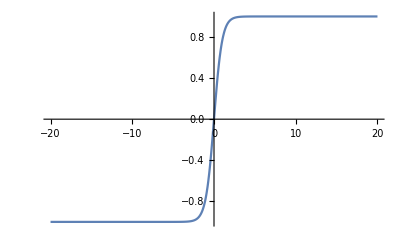

```mathematica
Plot[Tanh[z],{z,-20,20}]
```

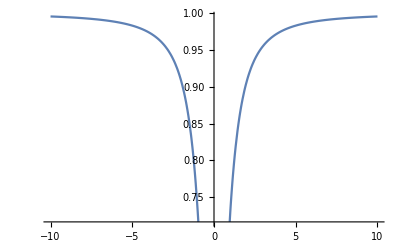

```mathematica
Plot[Hypergeometric2F1[1,(1+0.5)/2,(3+0.5)/2,-1/z^2],{z,-10,10}]
```

```mathematica
ComplexPlot[z^2+2 z Γ/π/.Γ->ArcTan[1/z]/(z^2-2),{z,-10ⅈ-5,10ⅈ+5}]
```

-Graphics-

```mathematica
Hypergeometric2F1[1,(1+0.5)/2,(3+0.5)/2,-1/z^2]
```

```mathematica
ComplexPlot[-ω^2+1+ⅈ 2 π ω Tanh[ω],{ω,-10ⅈ-5,10ⅈ+5}]
```

-Graphics-